## *** Figures for Intelligencer and L’Enseignement Mathématique (EPS, PDF)

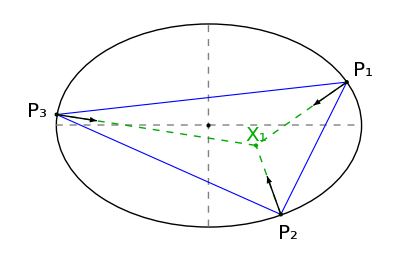

```mathematica
singleOrbitPlot=Module[{a=1.5,ons,deg1=25,poly1,ell,gr,grads1,clr={Blue,Thick},incClr="inc"/.ptClrs,lgt=.2,inc,fontSize=20},
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@deg1];
poly1=ons[[1]];
inc=getIncenterTrilin[First@ons,Third@ons];
grads1=ellGrad[a,Sequence@@#]&/@poly1;
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}},Black,Point@{0,0}},
{EdgeForm@clr,Polygon@poly1,Point@poly1,ellLabelPoints[a,poly1,"P",{fontSize},lgt]},
{incClr,Point@inc,Text[Style["X_1",fontSize],inc,{0,-1.5}]},
{Dashed,incClr,Thick,Line@{#,inc}&/@poly1},
{Black,Thick,MapThread[Arrow@{#1,#1+2lgt*norm@#2}&,{poly1,grads1}]}
}];
Show[{ell,gr}]]
```

```mathematica
export3["0000_single_orbit",singleOrbitPlot]
```

```mathematica
Clear@drThreeOrbits;
Options@drThreeOrbits={drX1locus->False,drX1s->True,drNorms->False,normLgt->.33};
drThreeOrbits[a_,OptionsPattern[]]:=Module[{ons,deg0=20,degStep=10,degRange=3,degs,poly1,caustic,ell,gr,grads1,clr={Blue,Thickness@.0075},incClr="inc"/.ptClrs,lgt=.33,incs,fontSize=20},
degs=(deg0+(#-1)*degStep)&/@Range@degRange;
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
poly1=ons[[1,1]];
incs=MapThread[getIncenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
caustic=Module[{o,n,s},Table[{o,n,s}=orbitNormals[a,toRad@i];getFeuerbachTrilin[o,s],{i,0,359}]];
grads1=ellGrad[a,Sequence@@#]&/@poly1;
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}},Black,Point@{0,0}},
{EdgeForm@clr,Polygon@poly1,Point[First/@First/@ons]},
{Brown,Thick,Line@caustic},
{MapThread[ellLabelTxt[a,#1,Style[#2,fontSize],.16]&,{First/@First/@ons,{"P","P'","P''"}}]},
If[OptionValue@drNorms,{Black,Thick,Arrowheads@Large,MapThread[Arrow@{#1,#1+OptionValue@normLgt norm@#2}&,{poly1,grads1}]},{}],
If[OptionValue@drX1s,{{incClr,MapThread[Text[Style[#1,fontSize],#2,#3]&,{{"X_1","X_1'","X_1''"},incs,{{-1.1,1.1},{-1.25,.5},{-1,-1.5}}}]},
{incClr,Point@incs(*,Thick,Line@incs*)}},{}],
{EdgeForm@{Dashed,Sequence@@clr},Polygon[First@#]&/@Rest@ons},
}];
Show[{ell,If[OptionValue@drX1locus,incenterLocus[a,π,{"exc"/.ptClrs,Thick}],{}],gr}]];
```

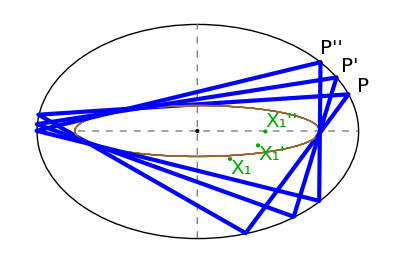

```mathematica
threeOrbitsPlot=drThreeOrbits[1.5,drX1locus->False,drX1s->True]
```

```mathematica
export3["0010_three_orbits",threeOrbitsPlot];
```

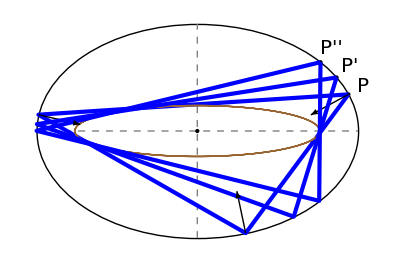

```mathematica
threeOrbitsPlotProof=drThreeOrbits[1.5,drX1locus->False,drX1s->False,drNorms->True,normLgt->.4]
```

```mathematica
export3["0010_three_orbits_proofs",threeOrbitsPlotProof];
```

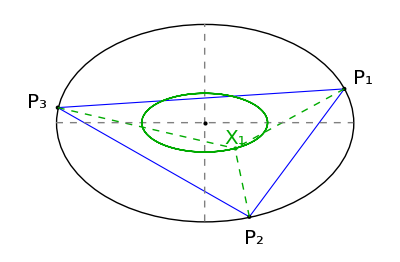

```mathematica
incenterLocusPlot=Module[{a=1.5,ons,o1,n1,s1,inc1,deg1=20,deg0=0,degStep=1,degRange=359,degs,poly1,ell,gr,grads1,clr={Blue,Thick},incClr="inc"/.ptClrs,lgt=.22,incs,fontSize=20},
degs=(deg0+(#-1)*degStep)&/@Range@degRange;
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
{o1,n1,s1}=orbitNormals[a,toRad@deg1];
inc1=getIncenterTrilin[o1,s1];
incs=MapThread[getIncenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
grads1=ellGrad[a,Sequence@@#]&/@poly1;
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{EdgeForm@clr,Polygon@o1,Point@o1,ellLabelPoints[a,o1,"P",fontSize,lgt]},
{Dashed,incClr,Thick,Line@{#,inc1}&/@o1},
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}},Black,Point@{0,0}},
{incClr,Thick,Line@incs},
{incClr,Point@inc1,Text[Style["X_1",fontSize],inc1,{0,-1.5}]}
}];
Show[{ell,gr}]]
```

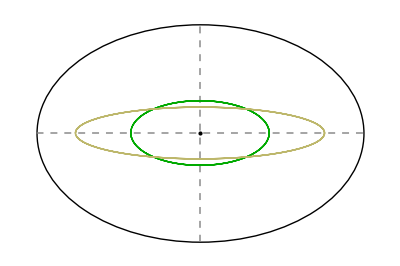

```mathematica
incenterLocusPlotClean=Module[{a=1.5,ons,o1,n1,s1,inc1,deg1=20,deg0=0,degStep=1,degRange=359,degs,poly1,ell,gr,grads1,clr={Blue,Thick},incClr="inc"/.ptClrs,lgt=.22,incs,fontSize=20,caustic},
degs=(deg0+(#-1)*degStep)&/@Range@degRange;
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
{o1,n1,s1}=orbitNormals[a,toRad@deg1];
inc1=getIncenterTrilin[o1,s1];
incs=MapThread[getIncenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
caustic=Module[{o,n,s},Table[{o,n,s}=orbitNormals[a,toRad@i];getFeuerbachTrilin[o,s],{i,0,359}]];
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
(*{EdgeForm@clr,Polygon@o1,Point@o1,ellLabelPoints[a,o1,"P",fontSize,lgt]},*)
(*{Dashed,incClr,Thick,Line@{#,inc1}&/@o1},*)
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}},Black,Point@{0,0}},
{incClr,Thick,Line@incs},
{"feu"/.ptClrs,Thick,Line@caustic}
(*,{incClr,Point@inc1,Text[Style["X_1",fontSize],inc1,{0,-1.5}]}*)
}];
Show[{ell,gr}]]
```

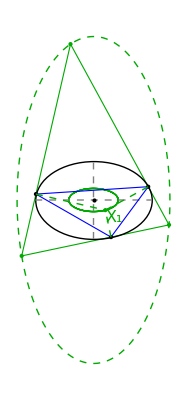

```mathematica
excenterLocusPlot=Module[{a=1.5,ons,deg1=20,poly1,ell,gr,grads1,clr={Blue,Thick},incClr="inc"/.ptClrs,lgt=.33,inc,exc,incExc,grExc,fontSize=20},
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@deg1];
exc=excentralTriangle[ons[[1]],ons[[3]]];
poly1=ons[[1]];
inc=getIncenterTrilin[First@ons,Third@ons];
incExc=Transpose@Module[{o,n,s},
Table[{o,n,s}=orbitNormals[a,toRad@i];{getIncenterTrilin[o,s],excentralTriangle[o,s][[1]]},{i,0,359}]];
grads1=ellGrad[a,Sequence@@#]&/@poly1;
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}},Black,Point@{0,0}},
{EdgeForm@clr,Polygon@poly1,Point@poly1},
{incClr,Point@inc,Text[Style["X_1",16],inc,{-1.5,.75}]},
{Dashed,incClr,Line@{#,inc}&/@poly1}
}];
grExc=Graphics[{Thick,FaceForm@None,EdgeForm@{Thick,incClr},incClr,PointSize@Large,Point@exc,Polygon@exc,Line@incExc[[1]],Dashed,Line@incExc[[2]]}];
Show[{grExc,ell,gr}]]
```

```mathematica
export3["0019_excenter_locus",excenterLocusPlot];
```

```mathematica
export3["0020_incenter_locus",incenterLocusPlot];
```

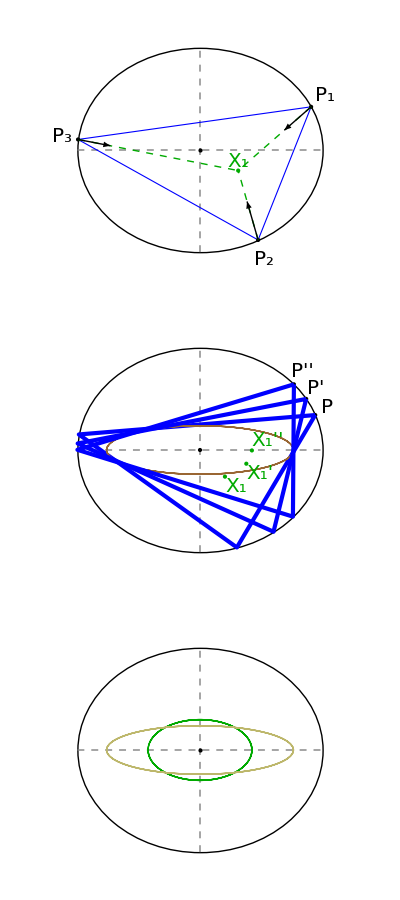
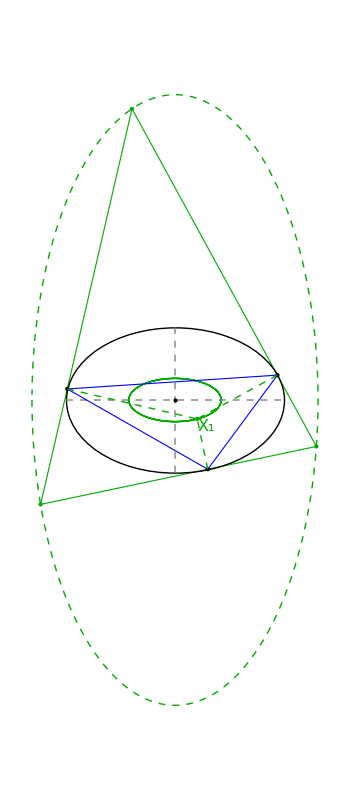
-Graphics- | -Graphics-

```mathematica
incenterLocusQuad=Grid[{{Grid[{Show[#,PlotRange->{{-2,2},{-1.2,1.2}},ImageSize->400]}&/@{singleOrbitPlot,threeOrbitsPlot,incenterLocusPlotClean},Spacings->0],Show[excenterLocusPlot,PlotRange->{Automatic,{-4.5,4.5}},ImageSize->350]}},Spacings->3,Frame->All]
```

```mathematica
export3["0021_incenter_locus_quad",incenterLocusQuad];
```

#### X26

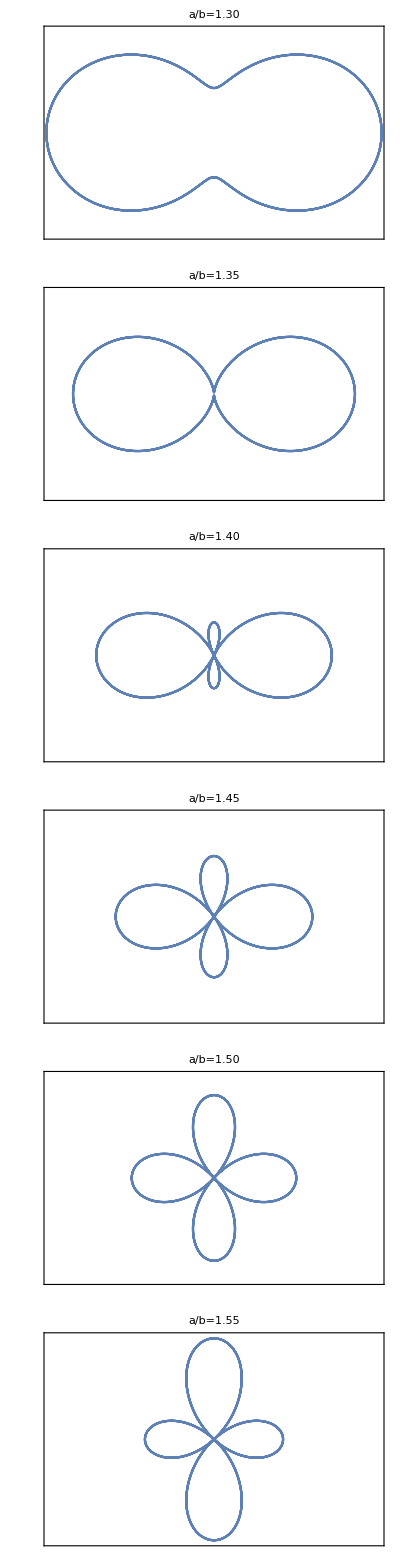

```mathematica
stereo26plot=Partition[Show[showX26[#,"proj"->"stereo"],PlotRange->{{-.7,.7},{-.5,.5}},Axes->True,Ticks->None,FrameTicks->None,ImageSize->190]&/@Range[1.3,1.55,.05],1]//Grid[#,Frame->All]&
```

```mathematica
x26plot=Show[plotX26[1.25,5.,xdispl->{-1.5,0}],PlotRange->All,ImageSize->800,Epilog->Inset[stereo26plot,{3.5,.4},Background->Directive[White,Opacity@.8]]]
```

-Graphics-

```mathematica
export3["0051_x26",x26plot]
```

#### X59

```mathematica
Clear@plotX59;
Options@plotX59={drX4->False,deg1->20.,x59displ->{0,-1.5},lgt->.22,degStep->.1,degMax->180.,thickness->Large,drPs->True};plotX59[a_,OptionsPattern[]]:=Module[{ons,o1,n1,s1,x59,x4,deg0=0.1,degs,poly1,ell,gr,grads1,clr=Blue,,pclr="x59"/.ptClrs,ps,fontSize=20},
degs=.01+Range[0,OptionValue@degMax-OptionValue@degStep,OptionValue@degStep];
ell=plotEll[a,{Thickness@OptionValue@thickness,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
{o1,n1,s1}=orbitNormals[a,toRad@OptionValue@deg1];
x59=getX59Trilin[o1,s1];
x4=getOrthocenterTrilin[o1,s1];
ps=MapThread[getX59Trilin[#1,#2]&,{First/@ons,Third/@ons}];
grads1=ellGrad[a,Sequence@@#]&/@poly1;
gr=Graphics[{FaceForm@None,PointSize@Large,Thickness@OptionValue@thickness,
{EdgeForm@{Thickness@OptionValue@thickness,clr},Polygon@o1,Point@o1,If[OptionValue@drPs,ellLabelPoints[a,o1,"P",fontSize,OptionValue@lgt],{}]},
(*{Dashed,pclr,Thick,Line@{#,p1}&/@o1},*)
{Dashed,Gray,Thick,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}(*,Point@{0,0}*)},
{pclr,Line@ps},
{pclr,Point@x59,Text[Style["X_59",fontSize],x59,OptionValue@x59displ(*,Background->Directive[Opacity@.66,White]*)]},
If[OptionValue@drX4,{Purple,Point@x4,Text[Style["X_4",fontSize],x4,{1,-1.25}]},{}]
}];
Show[{ell,gr},PlotLabel->Style["a/b="<>nfn[a,2]<>", t="<>nfn[OptionValue@deg1,1]<>"°",20]]];
```

```mathematica
ellPerimeterRamanujan[1.5,1]
```

7.93272

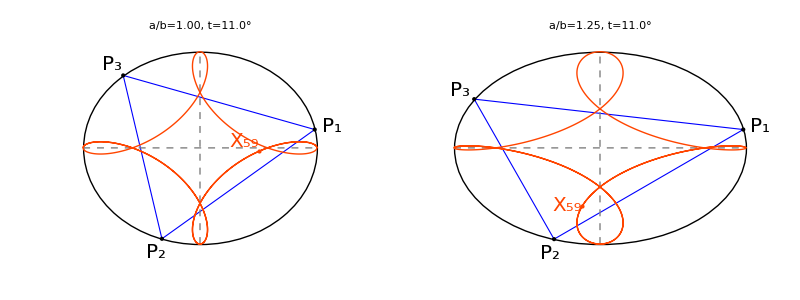

```mathematica
x59Plot=Module[{as},
Grid[{MapThread[Show[plotX59[#1,deg1->#3,x59displ->#2,lgt->.15],PlotRange->{{-1.4,1.4},{-1.3,1.1}},ImageSize->400]&,{{1.001,1.25},{{1.5,-.5},{1.5,0}},{11,11}}]}]
]
```

```mathematica
export3["0050_x59_locus",x59Plot];
```

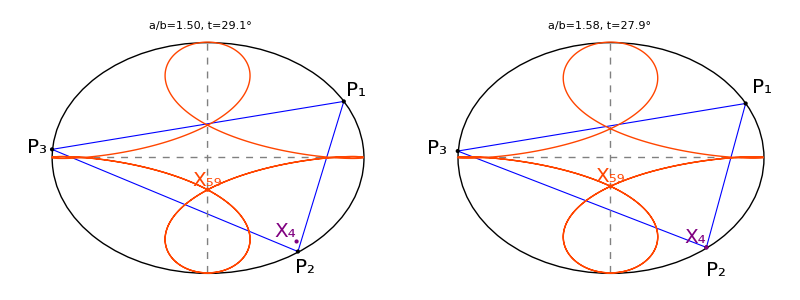

```mathematica
x59crossPlot=Grid[{Show[#,ImageSize->400]&/@{
plotX59[1.5,deg1->29.085,drX4->True,x59displ->{0,-1.5},lgt->.15],
plotX59[1.58005,deg1->27.9211,drX4->True]}}]
```

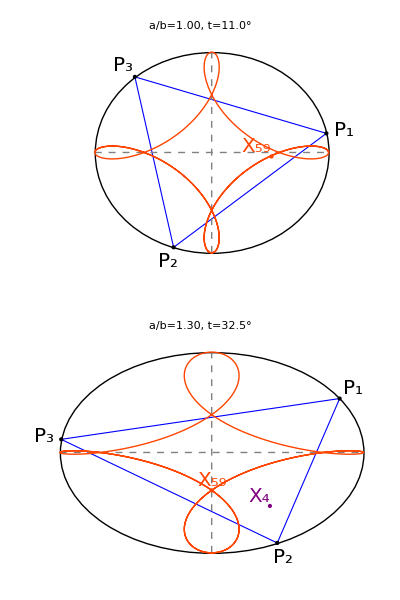
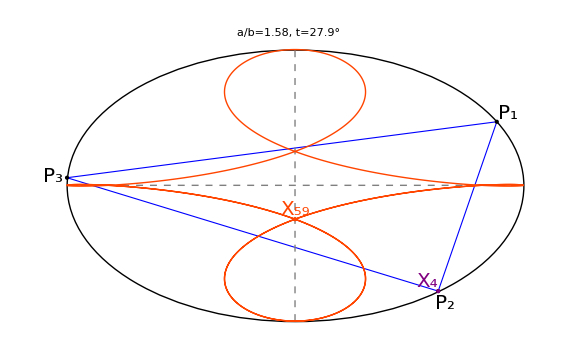
-Graphics- | -Graphics-

```mathematica
x59crossPlot3=Module[{p1,p2,p3,gr1},
p1=plotX59[1.001,deg1->11,x59displ->{1.5,-.66},lgt->.15];
p2=plotX59[1.3,deg1->32.52,drX4->True,x59displ->{0,-2},lgt->.15];
p3=plotX59[1.58005,deg1->27.9211,drX4->True,lgt->.1];
gr1=Grid[{#}&/@(Show[#,ImageSize->400,PlotRange->{{-1.5,1.3},{-1.2,1.1}}]&/@{p1,p2}),Spacings->0];
Grid[{{gr1,Show[p3,ImageSize->Large]}},Spacings->1,Frame->All]]
```

```mathematica
export3["0050_x59_center",x59crossPlot3];
```

```mathematica
Clear@x88motion;
Options@x88motion={drX4locus->False,x4disp->{-1.25,1.25},drSides->False};x88motion[a_,tDeg_,OptionsPattern[]]:=Module[{o1,n1,s1,x88,x4,x100,x1,poly1,ell,rho,gr,clr={Blue,Thick},lgt=.2,incClr="inc"/.ptClrs,x100Clr=Black,x88Clr="x88"/.ptClrs,ortClr="ort"/.ptClrs,x4locus,mid,sidesLab},
ell=plotEll[a,{Thick,Black}];
{o1,n1,s1}=orbitNormals[a,toRad@tDeg];
x1=getIncenterTrilin[o1,s1];
x100=getX100Trilin[o1,s1];
x88=getX88Trilin[o1,s1];
x4=getOrthocenterTrilin[o1,s1];
x4locus=If[OptionValue@drX4locus,Quiet@Module[{ons},ParametricPlot[ons=orbitNormals[a,t];getOrthocenterTrilin[ons[[1]],ons[[3]]],{t,0.01,π},PlotStyle->{Thick,ortClr}]],{}];
rho=magn[x1-x100]/magn[x1-x88];
mid=medialTriangle[o1,s1];
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{EdgeForm@incClr,FaceForm@{Opacity@.1,incClr}},
{EdgeForm@clr,Polygon@o1,Point@o1(*,ellLabelPoints[a,o1,"P",{Bold,16},.15]*)},
(*{Dashed,incClr,Line@{#,inc1}&/@o1},*)
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
{Dashed,Darker@Red,Thick,Line@{x100,x88}},
{incClr,Point@x1,Text[Style["X_1",20],x1,{0,-1.5}]},
{ortClr,Point@x4,Text[Style["X_4",20],x4,OptionValue@x4disp]},
{x100Clr,Point@x100,ellLabelTxt[a,x100,Style["X_100",20],lgt]},
{x88Clr,Point@x88,ellLabelTxt[a,x88,Style["X_88",20],lgt]},
If[OptionValue@drSides,{Blue,Point@mid,
ellLabelPointsSuffixb[a,a,mid,"s","="<>nfn[#,2]&/@s1,16]
(*ellLabelPoints[a,mid,"s",20,OptionValue@lgt]*)},{}]
}];
sidesLab=If[OptionValue@drSides,"\n(s_1,s_2,s_3)=("<>nfn[s1[[1]],2]<>","<>nfn[s1[[2]],2]<>","<>nfn[s1[[3]],2]<>")",""];
Show[{ell,x4locus,gr},PlotLabel->Style["a="<>nfn[a,2]<>", t="<>nfn[tDeg,2]<>"°, ρ="<>nfn[rho,2],{Black,20}]]]
```

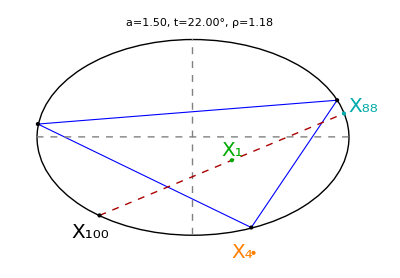

```mathematica
x88at15unalignedplot=x88motion[1.5,22,x4disp->{1.25,0},drSides->False]
```

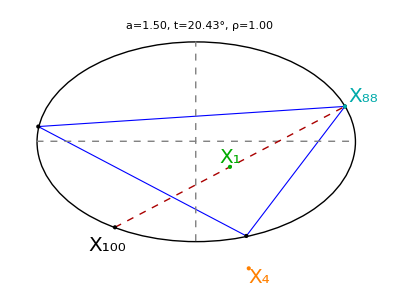

```mathematica
x88at15plot=x88motion[1.5,20.432,drSides->False]
```

### at 3:4:5 configuration

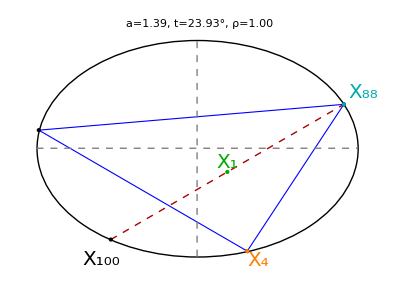

```mathematica
x88rightPlot=x88motion[1.3924,23.934,drSides->False]
```

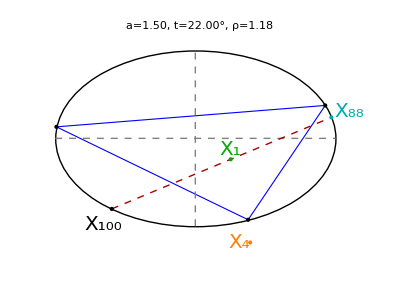
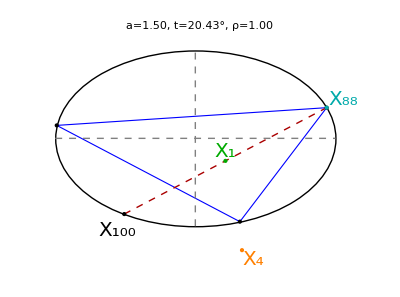
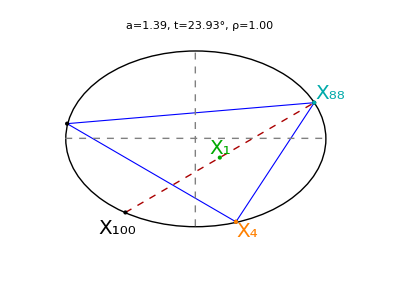
-Graphics- | -Graphics- | -Graphics-
(a) | (b) | (c)

```mathematica
x88both=Grid[{Show[#,PlotRange->{{-1.7,1.8},{-1.5,1.1}},ImageSize->400]&/@{x88at15unalignedplot,x88at15plot,x88rightPlot},Style[#,20]&/@{"(a)","(b)","(c)"}},Spacings->0]
```

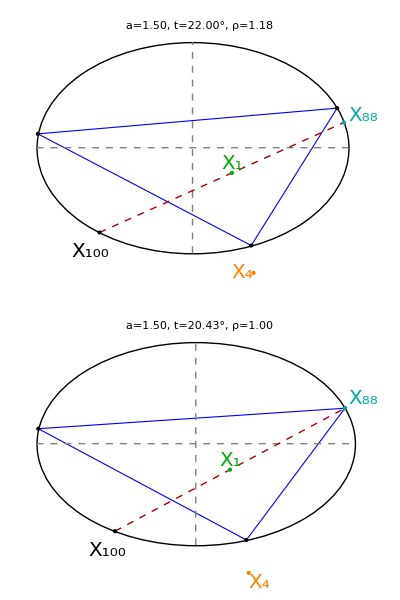
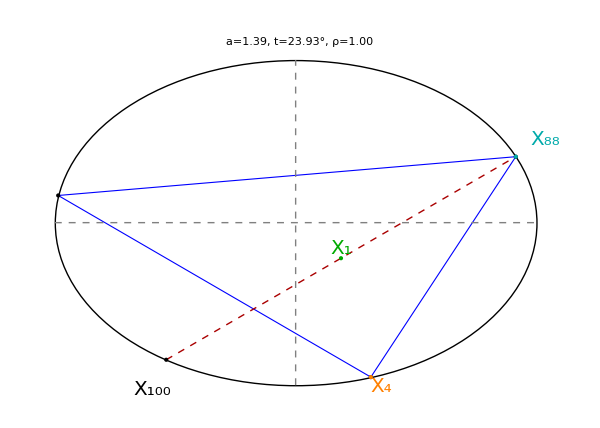
-Graphics- | -Graphics-

```mathematica
x88both2=Grid[{{Grid[{{Show[x88at15unalignedplot,ImageSize->400]},{Show[x88at15plot,ImageSize->400]}},Spacings->0],Show[x88rightPlot,ImageSize->600]}},Frame->All,Spacings->0]
```

```mathematica
export3["0052_x88_both",x88both2]
```

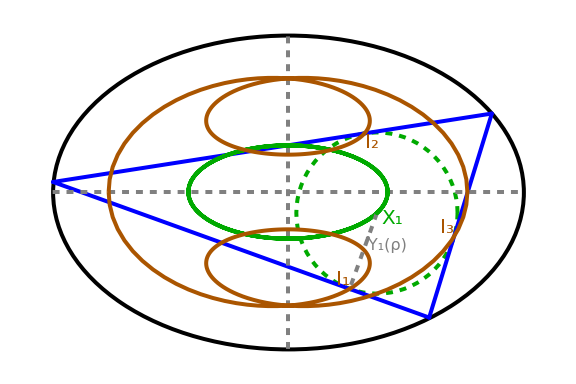

```mathematica
introPlot=Module[{a=1.5,ons,o1,n1,s1,inc1,peds1,deg100,deg1=30,degStep=1,degRange=360,degs,poly1,ell,gr,clr=Blue,incClr="inc"/.ptClrs,lgt=.33,incs,peds,pedClr=Darker@Orange,delta,a1,b1,thick=.005,rho=.33,convexComb},
degs=Range[0,degRange,degStep];
ell=plotEll[a,{Thickness@thick,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
{o1,n1,s1}=orbitNormals[a,toRad@deg1];
inc1=getIncenterTrilin[o1,s1];
peds1=intouchTriangle[o1,s1];
incs=getIncenterTrilin[#[[1]],#[[3]]]&/@ons;
peds=intouchTriangle[#[[1]],#[[3]]][[1]]&/@ons;
delta=a^4-a^2+1;
{a1,b1}={(delta-1)/a,(a^2-delta)};
convexComb=(1-rho)inc1+rho peds1[[1]];
gr=Graphics[{FaceForm@None,PointSize@Large,Thickness@thick,
{Dashed,incClr,Circle[inc1,magn[peds1[[1]]-inc1]]},
{EdgeForm@{Thickness@thick,clr},Polygon@o1,Blue,Point@o1},
(*{Dashed,incClr,Line@{#,inc1}&/@o1},*)
{Dashed,Gray,Thick,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
{incClr,Line@incs},
{pedClr,Point@peds1,Line@peds},
{Thickness@Large,Gray,Dashed,Line@{inc1,peds1[[1]]},Point@convexComb,Text[Style["Y_1(ρ)",16],convexComb,{-1.25,.5}]},
{pedClr,MapThread[Text[Style[#1,20],#2,#3]&,{
{"I_1","I_2","I_3"},
peds1,
{{.5,-1.5},{-1,1.25},{1.25,-1.5}}
}]},
{incClr,Point@inc1,ellLabelTxtb[a1,b1,inc1,Style["X_1",20],.1]}
}];
Show[{ell,gr},ImageSize->Large]]
```

```mathematica
export3["1020_incenter_locus",introPlot];
```

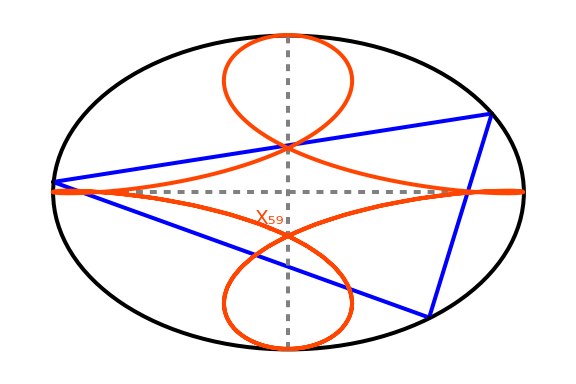

```mathematica
x59Plot1=
Show[plotX59[1.5,deg1->30.,x59displ->{-.25,-1.5},lgt->.15,degStep->.5,thickness->.005,drPs->False],PlotLabel->None,PlotRange->All,ImageSize->Large]
```

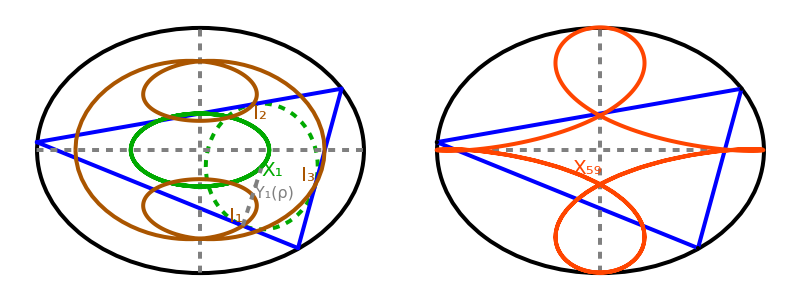

```mathematica
X1X59Plot=Grid[{{introPlot,x59Plot1}}]
```

```mathematica
export3["1021_x1_x59",X1X59Plot];
```

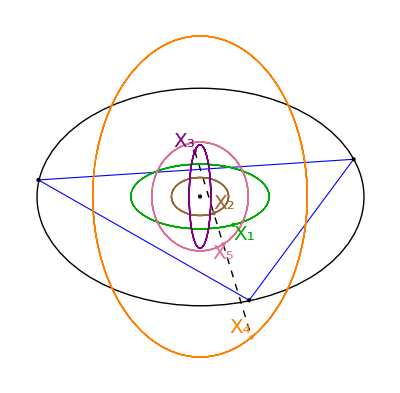

```mathematica
x12345Plot=Module[{a=1.5,ons,o1,n1,s1,inc1,bar1,cir1,ort1,,npc1,deg1=20,deg0=0,degStep=1,degRange=359,degs,poly1,ell,gr,clr={Blue,Thick},lgt=.33,incs,bars,cirs,orts,npcs,clrs,fontSize=20},
degs=(deg0+(#-1)*degStep)&/@Range@degRange;
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
{o1,n1,s1}=orbitNormals[a,toRad@deg1];
inc1=getIncenterTrilin[o1,s1];
bar1=getBarycenterTrilin[o1,s1];
cir1=getCircumcenterTrilin[o1,s1];
ort1=getOrthocenterTrilin[o1,s1];
npc1=getNinepointCenterTrilin[o1,s1];
incs=MapThread[getIncenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
bars=MapThread[getBarycenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
cirs=MapThread[getCircumcenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
orts=MapThread[getOrthocenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
npcs=MapThread[getNinepointCenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
clrs=#/.ptClrs&/@{"inc","bar","cir","ort","npc"};
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{EdgeForm@clr,Polygon@o1,Point@o1},
{Black,PointSize@Medium,Point@{0,0}},
{Black,Dashed,Line@{cir1,ort1}},
MapThread[{#1,Thick,Line@#2}&,{clrs,{incs,bars,cirs,orts,npcs}}],
MapThread[{#1,Point@#2,Text[Style[Subscript["X",#3],fontSize],#2,#4]}&,
{clrs,{inc1,bar1,cir1,ort1,npc1},{1,2,3,4,5},
{{-1.25,1.2},{-1.25,-1},{1.25,-.6},{1.25,-1.},{.25,1.25}}}]
}];
Show[{ell,gr}]]
```

```mathematica
export3["0030_x12345_locus",x12345Plot];
```

```mathematica
plotX40single=Module[{ϕ=(1+Sqrt@5)/2.,gold=RGBColor@({212,175,55}/255),pl},
pl=plotX40[ϕ,20.,lgt->.35,shortLabel->True,ellStyle->{gold,Thickness@.01}];
Show[pl,ImageSize->400,PlotRange->All,Epilog->{gold,Text[Style["ϕ",20],{ϕ+.2,.2}],Purple,Dashed,Line@{{0,1},{0,ϕ}},Line@{{0,-1},{0,-ϕ}},Text[Style["ϕ",20],{0,ϕ+.25}]}]]
```

-Graphics-

```mathematica
export3["00071_x40",plotX40single]
```

```mathematica
Clear@showTwoIsosceles;
Options@showTwoIsosceles={fontSize->20,dist1->.1,dist2->.1,drMirror->False,drMirrorLabels->False};
showTwoIsosceles[a_,OptionsPattern[]]:=Module[{ons0,ons1,ell,gr,locus,inc0,inc1},
ell=plotEll[a,{Thick,Black}];
ons0=orbitNormals[a,0.];
ons1=orbitNormals[a,π/2.];
locus=incenterLocus[a,π,{Thick,"exc"/.ptClrs}];
inc0=getIncenterTrilin[ons0[[1]],ons0[[3]]];
inc1=getIncenterTrilin[ons1[[1]],ons1[[3]]];
gr=Graphics@{FaceForm@None,PointSize@Large,
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
{EdgeForm@{Thick,Red},Polygon@ons0[[1]],Red,Point@ons0[[1]],Point@inc0,ellLabelTxt[-inc0[[1]],inc0,Style["X_1(0)",OptionValue@fontSize,Background->White],OptionValue@dist1],Text[Style["P_1(0)",OptionValue@fontSize],ons0[[1,1]],{-1.5,0},Background->White]},
If[OptionValue@drMirror,
{{EdgeForm@{Thick,Dashed,Red},Polygon@(flipX/@ons0[[1]]),Red,Point@(flipX/@ons0[[1]]),If[OptionValue@drMirrorLabels,{
Text[Style["P_1(t^*)",OptionValue@fontSize],flipX@ons0[[1,3]],{-1,-1}],
Text[Style["P_1(-t^*)",OptionValue@fontSize],flipX@ons0[[1,2]],{-1.15,1}],
Text[Style["P_1(π-t^*)",OptionValue@fontSize],ons0[[1,3]],{1,-1}]},{}]},
{EdgeForm@{Thick,Dashed,Blue},Polygon@(flipY/@ons1[[1]]),Blue,Point@(flipY/@ons1[[1]]),If[OptionValue@drMirrorLabels,{
Text[Style["P_1(t^(**))",OptionValue@fontSize],flipY@ons1[[1,2]],{-1.15,-1}],
Text[Style["P_1(-t^(**))",OptionValue@fontSize],ons1[[1,2]],{-1.15,1}],
Text[Style["P_1(π-t^(**))",OptionValue@fontSize],flipY@ons1[[1,3]],{1.15,-1}]
},{}]}},{}],
{EdgeForm@{Thick,Blue},Polygon@ons1[[1]],Blue,Point@ons1[[1]],Point@inc1,ellLabelTxtb[-inc0[[1]],inc1[[1]],inc1,Style["X_1(π/2)",OptionValue@fontSize,Background->White],OptionValue@dist2,inward->True],
Text[Style["P_1(π/2)",OptionValue@fontSize],ons1[[1,1]],{0,-1.5},Background->White]}};
Show[{ell,locus,gr},ImageSize->Large]];
```

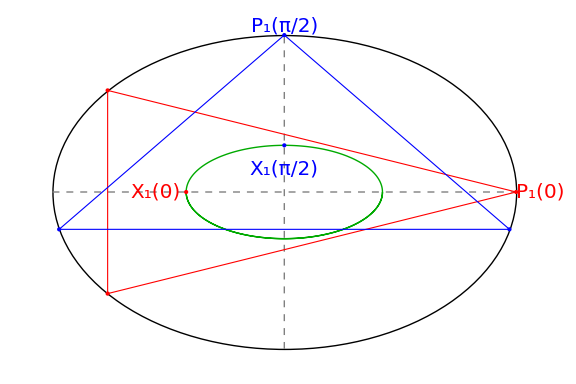

```mathematica
plotTwoIsosceles=showTwoIsosceles[1.5,dist1->.2,dist2->.15,drMirror->False]
```

```mathematica
export3["0072_two_isosceles",plotTwoIsosceles]
```

```mathematica
Limit[getJoachimsthal[a],{a->1}]
```

{(√3)/2}

```mathematica
Limit[getJoachimsthal[a],{a->∞}]
```

{0}

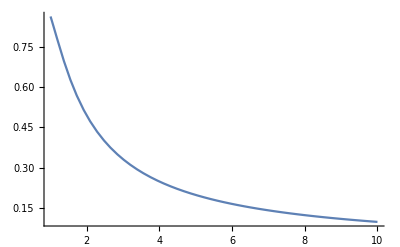

```mathematica
Plot[getJoachimsthal[a],{a,1.01,10}]
```

```mathematica
Clear@showTwoIsoscelesPosition;
Options@showTwoIsoscelesPosition={fontSize->20,dist1->.1,dist2->.1,drMirror->False};
showTwoIsoscelesPosition[a_,pos_(*1,2,3,4,5*),OptionsPattern[]]:=Module[{ell,onsList,locus,incList,δ,a1,b1,gr,ts,tss,tsStr,tsVal},
δ=Sqrt[a^4-a^2+1];
a1=(δ-1)/a;b1=(a^2-δ);
ts=ArcTan[Sqrt@(-a^2+2+2*δ)/a^2];
tss=ArcTan[Sqrt@3*Sqrt@(-2*a^2+1+2δ)/(3*a)];
tsStr={"-t^*","-t^(**)","0","t^(**)","t^*"};
tsVal={-ts,-tss,0.,tss,ts};
ell=plotEll[a,{Thick,Black}];
onsList=orbitNormals[a,#]&/@tsVal;
locus=Graphics[{Thick,"exc"/.ptClrs,Circle[{0,0},{a1,b1}]}];
incList=getIncenterTrilin[#[[1]],#[[3]]]&/@onsList;
gr=Graphics@{FaceForm@None,PointSize@Large,
{EdgeForm@{Dashed,Blue,Thick},Polygon[#[[1]]]&/@Drop[Drop[onsList,{pos}],{1}]},
{Blue,Point[#[[1,1]]]&/@Drop[onsList,{pos}]},
{EdgeForm@{Thickness@.005,Red},Polygon[#[[1]]]&/@Part[onsList,{pos}],Red,Point@onsList[[pos,1]]},
{Blue,MapThread[ellLabelTxt[a,#1[[1,1]],Style["P_1("<>#2<>")",OptionValue@fontSize],OptionValue@dist2]&,Drop[#,{pos}]&/@{onsList,tsStr}],
Red,ellLabelTxt[a,onsList[[pos,1,1]],Style["P_1("<>tsStr[[pos]]<>")",OptionValue@fontSize],OptionValue@dist2]},
(*
{Black,ellLabelTxt[a,o[[1]],Style["P_1(t)",fontSize],OptionValue@lgt]},
*)

{Darker@Green,Point@incList[[pos]],
ellLabelTxtb[a1,b1,incList[[pos]],Style["X_1("<>tsStr[[pos]]<>")",OptionValue@fontSize],OptionValue@dist1]}};
Show[{ell,locus,gr},ImageSize->Large]];
```

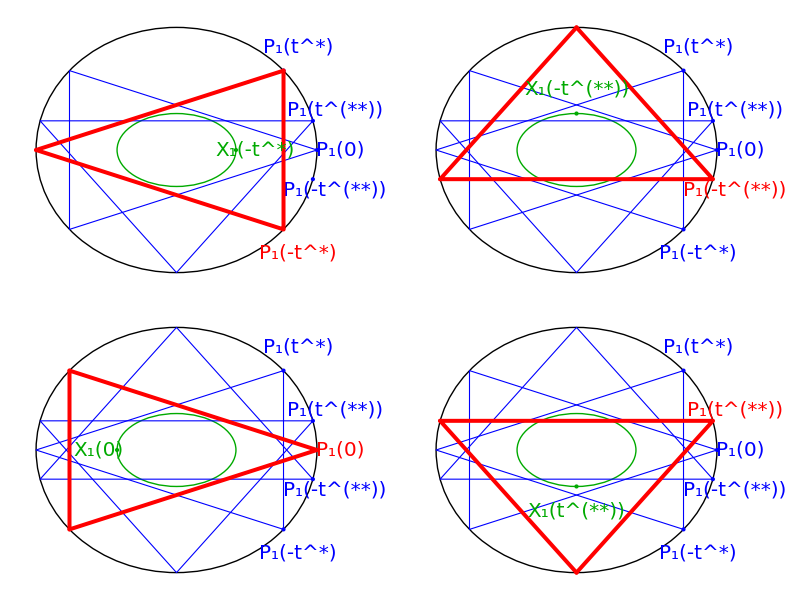

```mathematica
plotTwoIsoscelesTstar= Grid@Partition[showTwoIsoscelesPosition[1.5,#,dist1->.2,dist2->.25]&/@Range[5],2]
```

```mathematica
export3["0073_two_isosceles_tstar",plotTwoIsoscelesTstar]
```

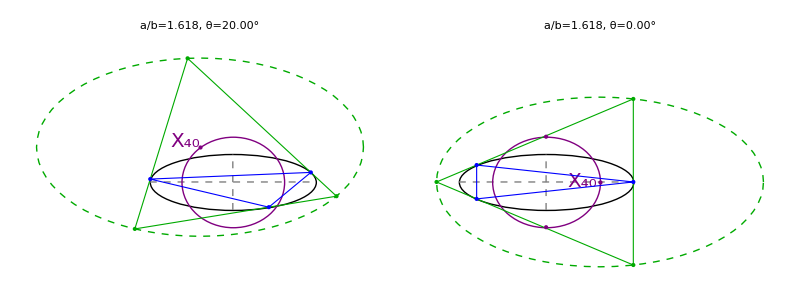

```mathematica
plotX40duo=Module[{ϕ=(1+Sqrt@5)/2.},
Grid[{Show[#,ImageSize->400,PlotRange->{Automatic,{-3.25,5}}]&/@{
plotX40[ϕ,20.,lgt->.35,shortLabel->True],
plotX40[ϕ,0.,lgt->.33,shortLabel->True,topBotVtx->True,inward0->True]}},Spacings->{3,0},Frame->None]]
```

```mathematica
Module[{ons,exc,phi=(1+Sqrt@5)/2,mtx},
ons=orbitNormals[phi,0];
exc=excentralTriangle[ons[[1]],ons[[3]]];
mtx=Append[#,1]&/@{exc[[2]],exc[[1]],{0,phi}};
mtx//MatrixForm]
```

(1.61803 | 2.9686 | 1
-2.03225 | 7.31093×10^-8 | 1
0 | 1/2 (1+√5) | 1)

```mathematica
frameX40combo[a_,tDeg_]:=Module[{touch,golden,combo},
touch=plotX40touch=Show[plotX40[Sqrt@2.,tDeg,shortLabel->True,lgt->.25]];
golden=Show[plotX40[(1+Sqrt@5.)/2,tDeg,shortLabel->True,lgt->.25]];
combo=Grid[{Show[#,ImageSize->Large,PlotRange->{{-4,2.75},{-2.5,4.7}}]&/@{touch,golden}},Spacings->0];
combo];
```

```mathematica
frameX40single[a_,tDeg_]:=Module[{golden},
golden=Show[plotX40[(1+Sqrt@5.)/2,tDeg,shortLabel->True,lgt->.25]];
Show[golden,ImageSize->Large,PlotRange->{{-4.5,4.5},{-5,5}}]];
```

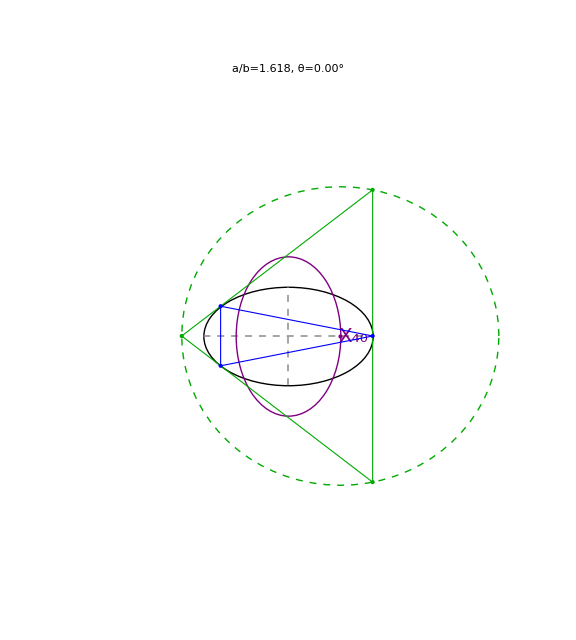

```mathematica
frameX40single[1.5,0]
```

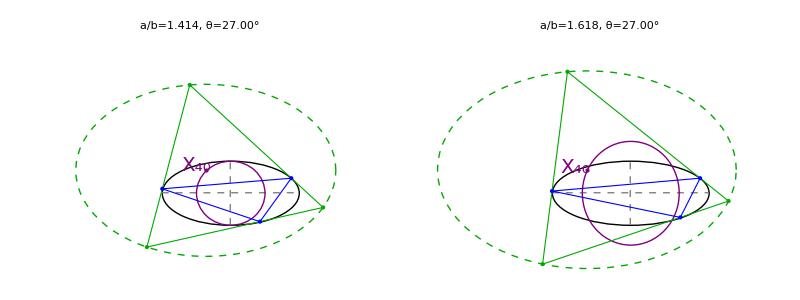

```mathematica
frameX40combo[1.5,27]
```

```mathematica
plotX40touch=Show[plotX40[Sqrt@2.,30,shortLabel->True]];
plotX40golden=Show[plotX40[(1+Sqrt@5.)/2,20,shortLabel->True]];
```

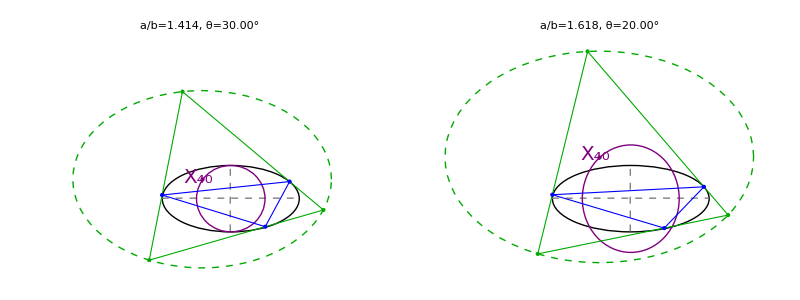

```mathematica
plotX40combo=Grid[{Show[#,ImageSize->Large,PlotRange->{{-4,2.75},{-2.25,4.7}}]&/@{plotX40touch,plotX40golden}},Spacings->0]
```

```mathematica
export3["0070_x40",plotX40combo]
```

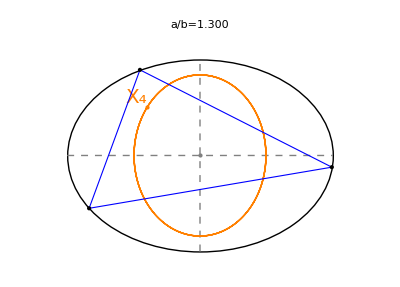
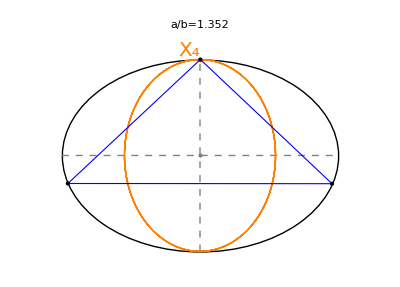
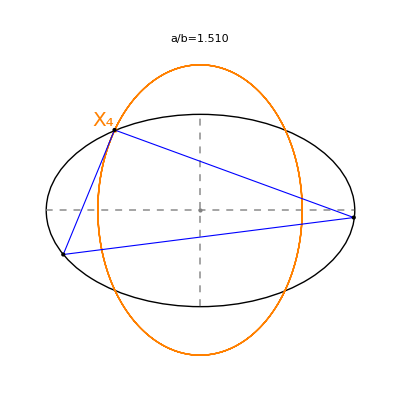
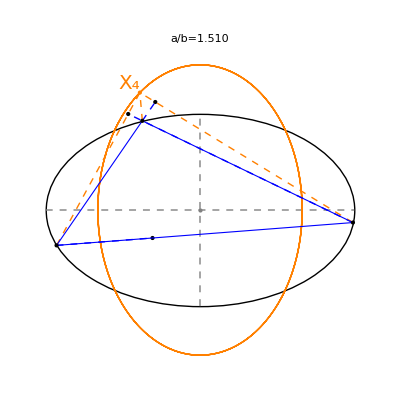
-Graphics-
(a) | -Graphics-
(b)
-Graphics-
(c) | -Graphics-
(d)

```mathematica
orthicLociPlot=Module[{orts},
orts={
showOrt[1.3,-7,drP1->False,p1Dist->.25],
showOrt[1.352,-17.1,drP1->False,p1Dist->.25],
showOrt[1.51,-9.0+4.5,drP1->False,p1Dist->.25],
showOrt[1.51,-9.0+1.5,drP1->False,p1Dist->.25,drAlts->True]
};
Grid[Partition[MapThread[Grid[{{Show[#1,PlotRange->{{-1.6,1.6},#3},ImageSize->400]},{#2}},Spacings->0]&,{orts,
Style[#,{Black,24}]&/@{"(a)","(b)","(c)","(d)"},{{-1.1,1.2},{-1.1,1.2},{-1.6,1.6},{-1.6,1.6}}}],2],Spacings->0]]
```

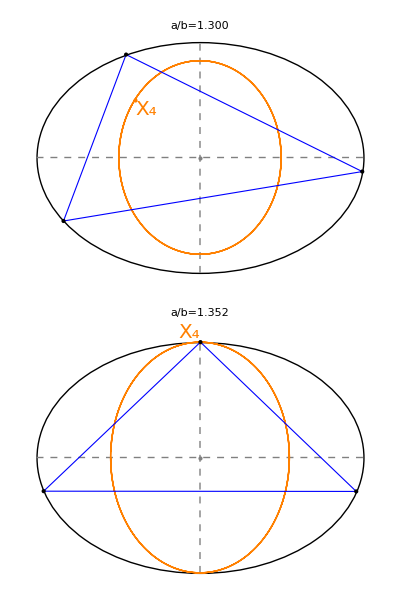
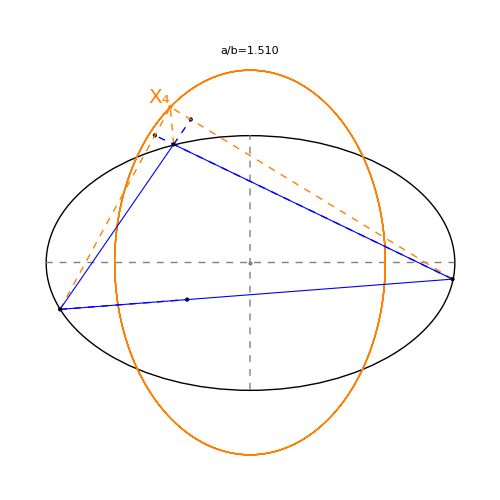
-Graphics- | -Graphics-

```mathematica
orthicLociPlot3=Module[{ort1,ort2,ort3},
ort1=showOrt[1.3,-7,drP1->False,p1Dist->.25,x4displ->{-1,1}];
ort2=showOrt[1.352,-17.1,drP1->False,p1Dist->.25];
ort3=showOrt[1.51,-9.0+1.5,drP1->False,p1Dist->.25,drAlts->True];
Grid[{{Grid[{{Show[ort1,ImageSize->300]},{Show[ort2,ImageSize->300]}},Spacings->0],Show[ort3,ImageSize->500]}},Spacings->0,Frame->All]]
```

```mathematica
export3["0045_ort_loci",orthicLociPlot3];
```

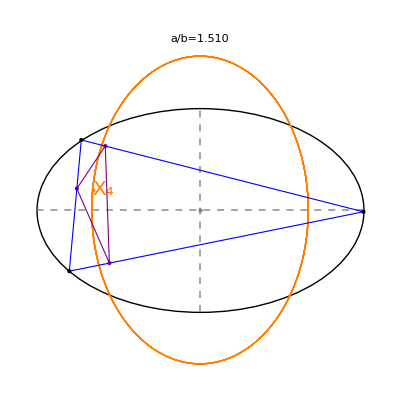
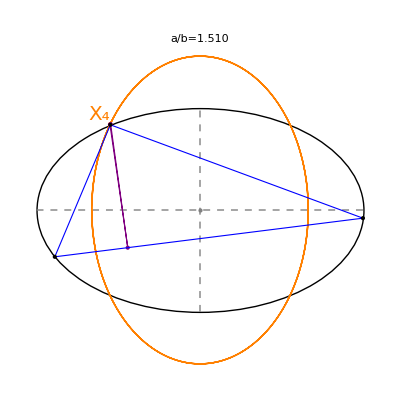
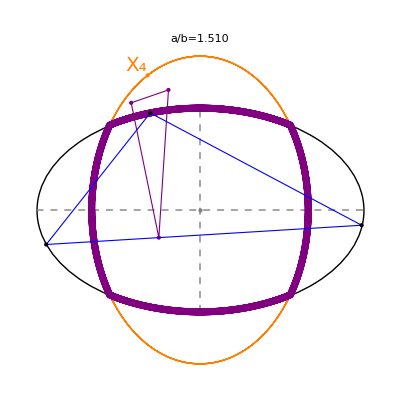
-Graphics- | -Graphics- | -Graphics-
(a) | (b) | (c)

```mathematica
orthicLociKinkPlot=Grid[{Show[#,ImageSize->400]&/@{
showOrt[1.51,-1,drP1->False,p1Dist->.25,drOrthic->True,x4displ->{-1.5,0}],
showOrt[1.51,-9.1+4.5,drP1->False,p1Dist->.25,drOrthic->True],
showOrt[1.51,-13.1+4.5,drP1->False,p1Dist->.25,drOrthic->True,drOrthicLocus->True]},
Style[#,{Black,24}]&/@{"(a)","(b)","(c)"}}]
```

```mathematica
export3["0045_ort_loci_kink",orthicLociKinkPlot];
```

```mathematica
Clear@showMit;
Options@showMit={drEll->True,drNormals->False,drVtx->False,drExt->False,drFeuTri->False,lgt->.33,drMs->True,mSize->12,drCaustic->False,drExcPerps->False,drAxes->True};
showMit[a_,deg1_,OptionsPattern[]]:=Module[{ons,poly1,ell,gr,ext,meds,grads1,x5,feuTri,clr={Blue,Thick},incClr="inc"/.ptClrs,exc,mit,grExc,caustic},
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@deg1];
exc=excentralTriangle[ons[[1]],ons[[3]]];
ext=extouchTriangle[ons[[1]],ons[[3]]];
x5=getNinepointCenterTrilin[ons[[1]],ons[[3]]];
feuTri=feuerbachTriangle[ons[[1]],ons[[3]]];
poly1=ons[[1]];
meds=getMedians@@poly1;
grads1=ellGrad[a,Sequence@@#]&/@poly1;
caustic=Module[{o,n,s},Table[{o,n,s}=orbitNormals[a,toRad@i];getFeuerbachTrilin[o,s],{i,0,359}]];
gr=Graphics[{clr,FaceForm@None,PointSize@Large,Arrowheads->Medium,
If[OptionValue@drAxes&&OptionValue@drEll,{Dashed,Black,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},{}],
If[OptionValue@drNormals,{Black,MapThread[Arrow@{#1,#1+OptionValue@lgt*norm[#2]}&,{poly1,grads1}]},{}],
{EdgeForm@clr,Polygon@poly1,Point@poly1},
If[OptionValue@drExcPerps,{Darker@Green,Dashed,Thick,MapThread[Line@{#1,#2}&,{exc,ext}]},{}],
If[OptionValue@drCaustic,{"feu"/.ptClrs,Thick,Line@caustic},{}],
If[OptionValue@drExt,{Darker@Green,Point@ext,
ellLabelPointsbInward[2a,a,ext,"e",OptionValue@mSize,OptionValue@lgt/2],
ellLabelPoints[2a,exc,"P'",OptionValue@mSize,OptionValue@lgt/2],
Dashed,Thick,MapThread[Circle[#1,magn[#1-#2]]&,{exc,ext}]},{}],
{Red,Dashed,Line@{#,ray[#,-#,1.5]}&/@exc},
If[OptionValue@drFeuTri,
{Pink,Thick,Circle[x5,magn[feuTri[[1]]-x5]],PointSize@Large,Point@feuTri},{}],
{Blue,Point@meds,If[OptionValue@drMs,MapThread[Text[Style[Subscript["M",#2],OptionValue@mSize],#1,#3]&,{meds,Range@Length@meds,
{{1,-1.5},{-1.5,-1.25},{-1.5,1.2}}}],{}]},
{Red,Point@{0,0},Text[Style["X_9",OptionValue@mSize],{0,0},{-1.5,-1.25}]},
If[OptionValue@drVtx,{Black,ellLabelPoints[a,poly1,"P",OptionValue@mSize,OptionValue@lgt/2]},,{}]
}];
grExc=Graphics[{Thick,FaceForm@None,EdgeForm@{Thick,incClr},incClr,PointSize@Large,Point@exc,Polygon@exc}];
Show[{grExc,If[OptionValue@drEll,ell,{}],gr},PlotRange->{{-2.2,2.2},{-4.2,4.2}},ImageSize->Large]]
```

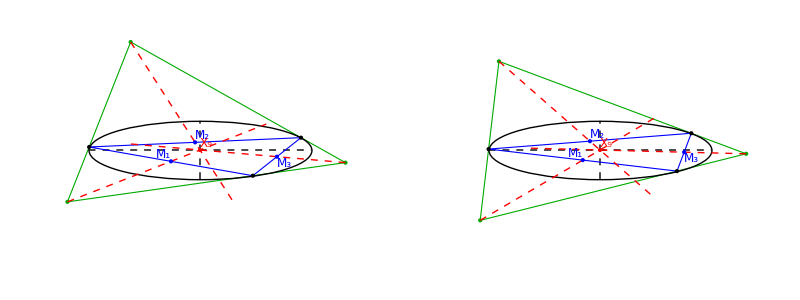

```mathematica
Grid[{showMit[1.5,#]&/@{25,35}}]
```

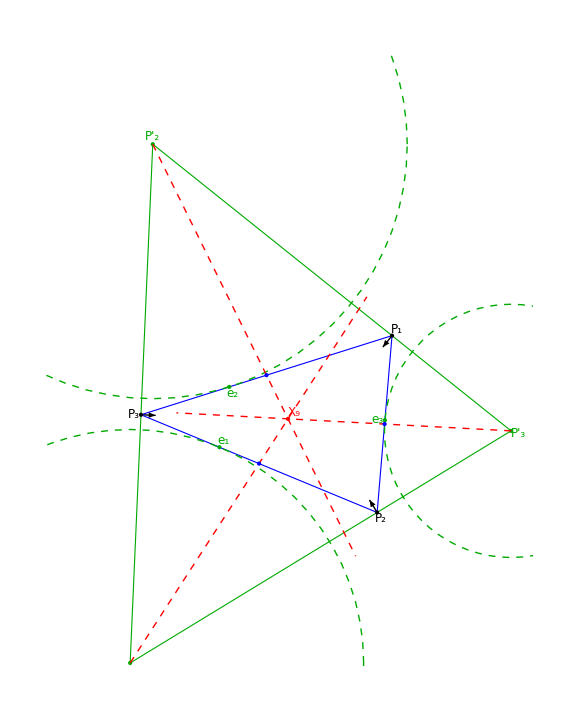

```mathematica
mittenExcPlot=Show[showMit[1.25,45,drEll->False,drNormals->True,lgt->.125,drVtx->True,drExt->True,drFeuTri->False,drMs->False],PlotRange->{{-2,2},{-2,3}},ImageMargins->10]
```

```mathematica
export3["0036_mittenExcPlot",mittenExcPlot];
```

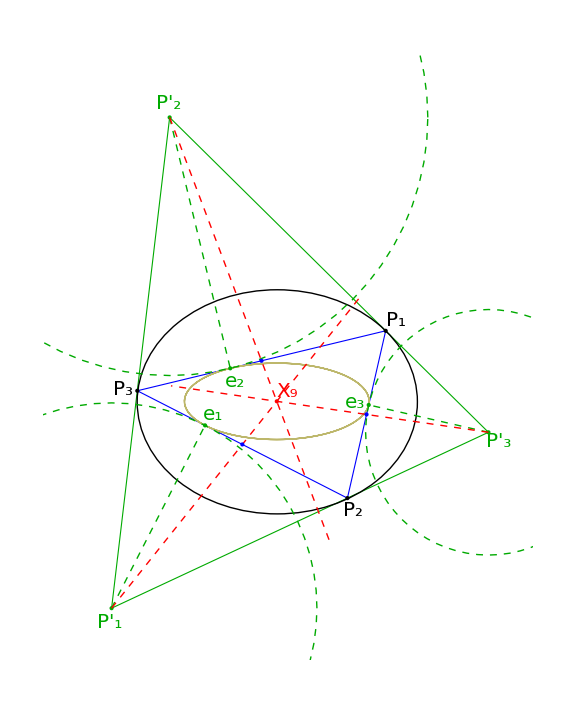

```mathematica
mittenExcPerpPlot=Show[showMit[1.25,39,drEll->True,drNormals->False,lgt->.25,drVtx->True,drExt->True,drMs->False,mSize->20,drCaustic->True,drExcPerps->True,drAxes->False],PlotRange->{{-2,2.2},{-2.2,3}},ImageMargins->10]
```

```mathematica
export3["0037_excenter_perps",mittenExcPerpPlot];
```

```mathematica
Clear@showMitScaled;showMitScaled[a_,deg1_,xScale_]:=Module[{ons,poly1,ell,gr,meds,clr={Blue,Thick},incClr="inc"/.ptClrs,lgt=.33,exc,mit,grExc},
ell=plotEll[a/xScale,{Thick,Black}];
ons=orbitNormals[a,toRad@deg1];
exc={#[[1]]/xScale,#[[2]]}&/@excentralTriangle[ons[[1]],ons[[3]]];
poly1={#[[1]]/xScale,#[[2]]}&/@ ons[[1]];
meds=getMedians@@poly1;
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{Dashed,Black,Line@{{-a/xScale,0},{a/xScale,0}},Line@{{0,-1},{0,1}}},
{EdgeForm@clr,Polygon@poly1,Point@poly1},
{Red,Dashed,Line@{#,ray[#,-#,1.5]}&/@exc},
{Blue,Point@meds,MapThread[Text[Style[Subscript["M",#2],20],#1,#3]&,{meds,Range@Length@meds,
{{.75,-1.5},{1.5,-1},{1.25,1}}}]},
{Red,Point@{0,0},Text[Style["X_9",{Bold,20}],{0,0},{-1.5,-1.25}]}
}];
grExc=Graphics[{Thick,FaceForm@None,EdgeForm@{Thick,incClr},incClr,PointSize@Large,Point@exc,Polygon@exc}];
Show[{grExc,ell,gr},PlotRange->{Automatic,{-2.75,3.75}},ImageSize->Large]]
```

```mathematica
(*Grid[{MapThread[showMitScaled[1.5,#1,#2]&,{{25,35,35},{1,1,1.5}}]}]*)
```

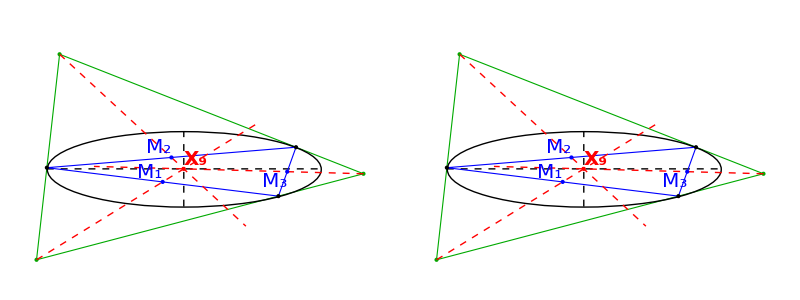

```mathematica
olgaPlot=Grid[{MapThread[showMitScaled[1.5,#1,#2]&,{{35,35},{1,1.5}}]}]
```

```mathematica
export3["0051_mitten_proof",olgaPlot];
```

```mathematica
Clear@showConstrs;
Options@showConstrs={drVtx->False,drX1->False,drX2->False,drX3->False,drX4->False,drX5->False,drX11->False,lgt->.33};
showConstrs[a_,deg1_,OptionsPattern[]]:=Module[{o,n,s,gr0,xn,feet,clr=Blue,txtStyle={Background->White,30},txtStyle2={30}},
{o,n,s}=orbitNormals[a,toRad@deg1];
gr0=Graphics[{clr,FaceForm@None,PointSize@Large,
{EdgeForm@{Thick,clr},Polygon@o,clr,Point@o},
If[OptionValue@drX1,Module[{int},
xn=getIncenterTrilin[o,s];
int=intouchTriangle[o,s];
feet=incentralTriangle[o,s];
{Black,
{Dashed,MapThread[Line@{#1,#2}&,{o,feet}]},
{Darker@Green,PointSize@Medium,Point@int,Thick,Circle[xn,magn[xn-int[[1]]]]},
Darker@Green,PointSize@Large,Point@xn,Text[Style["X_1",txtStyle],xn,{-1.25,-1.25}]}],{}],
If[OptionValue@drX2,
xn=getBarycenterTrilin[o,s];
feet=medialTriangle[o,s];
{Black,Dashed,MapThread[Line@{#1,#2}&,{o,feet}],
{EdgeForm@{Thick,Red},FaceForm@None,Polygon@feet},{PointSize@Medium,Point@feet},
{PointSize@Medium,Point@feet},
Brown,PointSize@Large,Point@xn,Text[Style["X_2",txtStyle],xn,{-1.25,-1.25}]},{}],
If[OptionValue@drX3,
xn=getCircumcenterTrilin[o,s];
feet=medialTriangle[o,s];
{Black,{Dashed,Line@{xn,#}&/@feet},{PointSize@Medium,Point@feet},
Purple,PointSize@Large,Point@xn,Thick,Circle[xn,magn[xn-o[[1]]]],Text[Style["X_3",txtStyle],xn,{-1.25,-1.25}]},{}],
If[OptionValue@drX4,
xn=getOrthocenterTrilin[o,s];
feet=orthicTriangle[o,s];
{Black,Dashed,MapThread[Line@{#1,#2}&,{o,feet}],
{EdgeForm@{Thick,Orange},FaceForm@None,Polygon@feet},{PointSize@Medium,Point@feet},
Darker@Orange,PointSize@Large,Point@xn,Text[Style["X_4",txtStyle],xn,{1.25,.5}]},{}],
If[OptionValue@drX5,
Module[{orthic,euler},
xn=getNinepointCenterTrilin[o,s];
feet=medialTriangle[o,s];
orthic=orthicTriangle[o,s];
euler=eulerTriangle[o,s];
{Black,
{Dashed,MapThread[Line@{#1,#2}&,{o,orthic}]},
{Pink,PointSize@Large,Point@xn,Thick,Circle[xn,magn[xn-feet[[1]]]],Text[Style["X_5",txtStyle],xn,{-1.25,-1.25}]},
{PointSize@Medium,Point@feet,Point@orthic,Point@euler}}],{}],
If[OptionValue@drX11,
Module[{x1,x5,intouch,medial},
x1=getIncenterTrilin[o,s];
intouch=intouchTriangle[o,s];
medial=medialTriangle[o,s];
x5=getNinepointCenterTrilin[o,s];
xn=getFeuerbachTrilin[o,s];
{
{Black,Dashed,Line@{x5,xn}},
{Darker@Green,PointSize@Large,Point@intouch,Point@x1,Thick,Circle[x1,magn[x1-intouch[[1]]]],Text[Style["X_1",txtStyle2],x1,{.5,1.25}]},
{Pink,PointSize@Large,Point@medial,Point@x5,Thick,Circle[x5,magn[x5-medial[[1]]]],Text[Style["X_5",txtStyle2],x5,{-1.25,-1.25}]},
{Black,PointSize@Large,Point@xn,Text[Style["X_11",txtStyle],xn,{-.75,1.15}]}}],{}],
If[OptionValue@drVtx,{Black,ellLabelPoints[a,o,"P",txtStyle,OptionValue@lgt/2]},,{}]
}];
Show[gr0,ImageSize->300]];
```

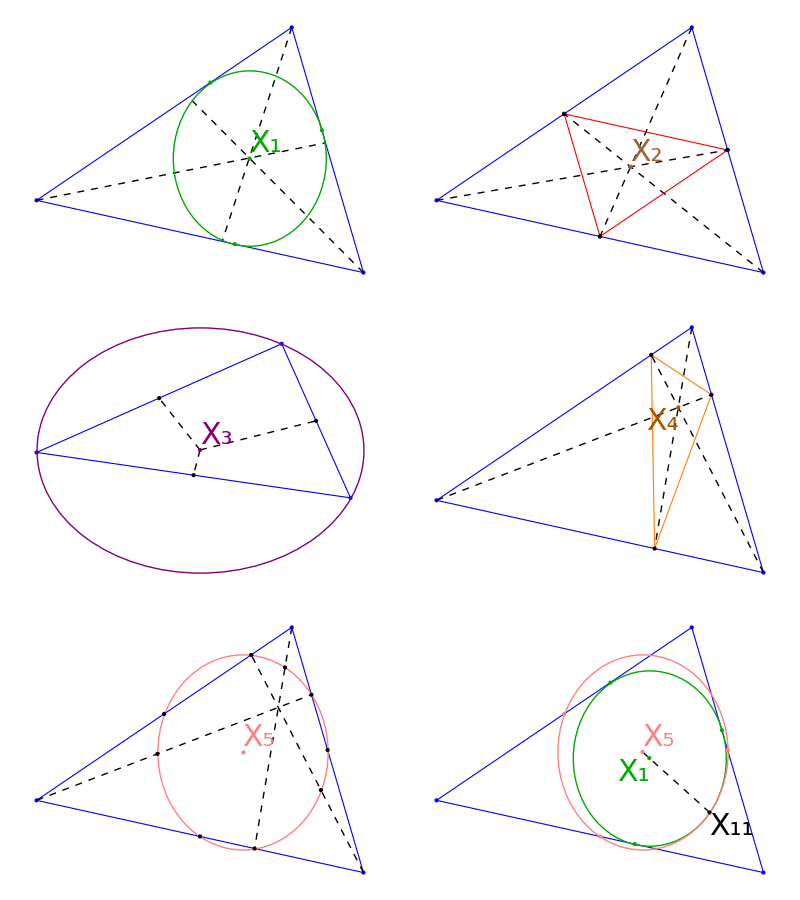
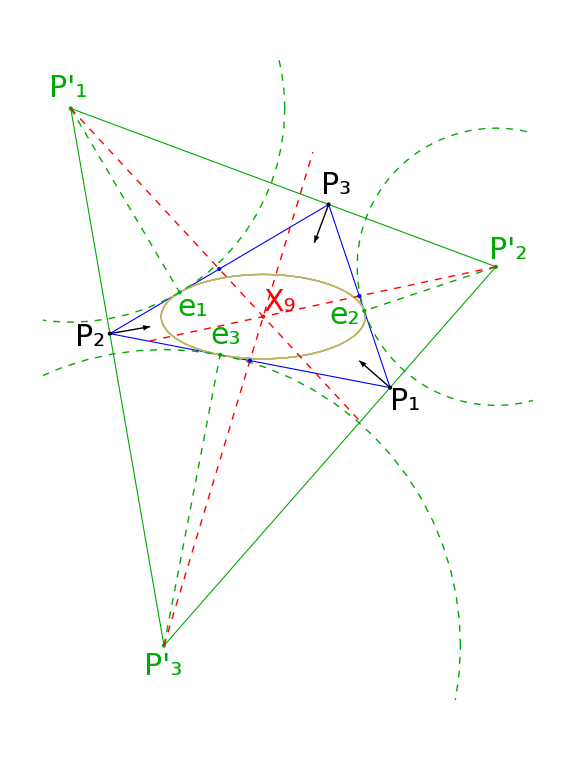
-Graphics- | -Graphics-

```mathematica
constrPlot=Module[{a=1.25,ang=-35,mit,gr1},
mit=Show[showMit[a,ang,drEll->False,drNormals->True,lgt->.33,drVtx->True,drExt->True,drFeuTri->False,drMs->False,mSize->30,drExcPerps->True,drCaustic->True],PlotRange->{{-1.7,2.1},{-3,2}}];
gr1=Grid[{
{showConstrs[a,ang,drX1->True],showConstrs[a,ang,drX2->True]},
{showConstrs[a,ang,drX3->True],showConstrs[a,ang,drX4->True]},
{showConstrs[a,ang,drX5->True],showConstrs[a,ang,drX11->True]}
}];
Grid[{{gr1,mit}},Frame->All]]
```

```mathematica
export3["0039_constr",constrPlot]
```

```mathematica
get12345plot[a_,deg1_]:=Module[{ons,o1,n1,s1,inc1,bar1,cir1,ort1,,npc1,deg0=0,degStep=1,degRange=359,degs,poly1,ell,gr,grads1,clr={Blue,Thick},lgt=.33,incs,bars,cirs,orts,npcs,clrs,fontSize=20},
degs=(deg0+(#-1)*degStep)&/@Range@degRange;
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
{o1,n1,s1}=orbitNormals[a,toRad@deg1];
inc1=getIncenterTrilin[o1,s1];
bar1=getBarycenterTrilin[o1,s1];
cir1=getCircumcenterTrilin[o1,s1];
ort1=getOrthocenterTrilin[o1,s1];
npc1=getNinepointCenterTrilin[o1,s1];
incs=MapThread[getIncenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
bars=MapThread[getBarycenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
cirs=MapThread[getCircumcenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
orts=MapThread[getOrthocenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
npcs=MapThread[getNinepointCenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
grads1=ellGrad[a,Sequence@@#]&/@poly1;
clrs=#/.ptClrs&/@{"inc","bar","cir","ort","npc"};
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
{EdgeForm@clr,Polygon@o1,Point@o1},
{Black,PointSize@Medium,Point@{0,0}},
{Black,Thick,Dashed,Line@{cir1,ort1}},
MapThread[{#1,Thick,Line@#2}&,{clrs,{incs,bars,cirs,orts,npcs}}],
MapThread[{#1,Point@#2,Text[Style[Subscript["X",#3],fontSize,Background->Directive[White,Opacity@.5]],#2,#4]}&,
{clrs,{inc1,bar1,cir1,ort1,npc1},{1,2,3,4,5},
{{-1.25,1.2},{-1.25,-1},{1.25,-.6},{1.5,-1.},{.5,1.25}}}]
}];
Show[{ell,gr}]]
```

```mathematica
Clear@showX11andX100;
Options@showX11andX100={lgt->.125};showX11andX100[a_,deg1_,OptionsPattern[]]:=Module[{o,n,s,ell,gr,x11,x100,x2,clr={Blue,Thick},mit,ctrs,rhat,rads,caustic,act,actSides,actCtrs,actRads,extouch,fontSize=20},
ell=plotEll[a,{Thick,Black}];
{o,n,s}=orbitNormals[a,toRad@deg1];
ctrs={getIncenterTrilin[o,s],getNinepointCenterTrilin[o,s]};
rads={getInradius@s,getNinepointCircleRadius@s};
caustic=Module[{o2,n2,s2},Table[{o2,n2,s2}=orbitNormals[a,toRad@i];getFeuerbachTrilin[o2,s2],{i,0,359}]];
rhat=rot[{1,0},toRad@25];
x11=getFeuerbachTrilin[o,s];
x100=getX100Trilin[o,s];
act=anticomplementaryTriangle[o,s];
actSides=triLengthsRL@act;
actCtrs={getIncenterTrilin[act,actSides],getNinepointCenterTrilin[act,actSides]};
actRads={getInradius@actSides,getNinepointCircleRadius@actSides};
extouch=extouchTriangle[o,s];
x2=getBarycenterTrilin[o,s];
gr=Graphics[{clr,FaceForm@None,PointSize@Large,Arrowheads@Medium,
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
{EdgeForm@clr,Polygon@o},
MapThread[{#1/.ptClrs,Thick(*Point@#2,Text[Style[Subscript["X",#4],{Bold,16}],#2,{0,-1.5}]*),Circle[#2,#3]}&,{{"inc","npc"},ctrs,rads,{1,5}}],
{Red,Point@{0,0},Text[Style["X_9",fontSize],{0,0},{-1.25,-1.}]},
{Black,Point@o},
{"feu"/.ptClrs,Thick,Line@caustic},
{Black,ellLabelTxt[a,o[[1]],Style["P_1(t)",fontSize],OptionValue@lgt]},
(*{EdgeForm@{Dashed,Blue,Thick},Polygon@act},*)
{"bar"/.ptClrs,Point@x2,Dashed,Thick,Line@{x11,x100},Text[Style["X_2",fontSize],x2,{-1.25,1.1}]},
(*MapThread[{#1/.ptClrs,Dashed,Thick,Circle[#2,#3]}&,{{"inc","npc"},actCtrs,actRads,{1,5}}],*)
{Black,Point@x100,ellLabelTxt[a,x100,Style["X_100",fontSize],.1],Point@x11,Text[Style["X_11",fontSize,Background->Directive[White,Opacity@.6]],x11,{-1.,-1.25}]},
{"inc"/.ptClrs,Point@extouch,ellLabelPointsb[2a,a,extouch,"e",fontSize,0.15]}
}];
Show[{ell,gr},ImageSize->Large]];
```

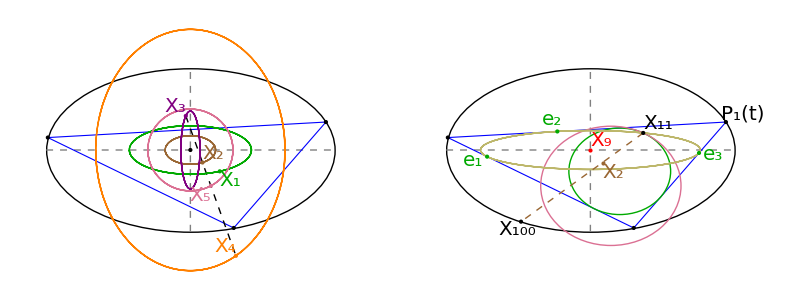

```mathematica
x12345feuerPlot=Grid[{Show[#,PlotRange->{{-1.6,1.8},{-1.5,1.5}},ImageSize->400]&/@{get12345plot[1.5,20],showX11andX100[1.5,20.,lgt->.2]}},Spacings->0]
```

```mathematica
export3["0030_x12345_feuerbach_combo",x12345feuerPlot]
```

```mathematica
Clear@showAntiCompl;
Options@showAntiCompl={"x100displ"->.15,"drCirc"->False};showAntiCompl[a_,deg1_,OptionsPattern[]]:=Module[{o,n,s,ell,gr,x11,x100,x2,clr={Blue,Thick},lgt=.33,mit,ctrs,rhat,rads,caustic,act,actInc,actInradius,actSides,actCtrs,actRads,actIntouch,ext},
ell=plotEll[a,{Thick,Black}];
{o,n,s}=orbitNormals[a,toRad@deg1];
ctrs={getIncenterTrilin[o,s],getNinepointCenterTrilin[o,s]};
rads={getInradius@s,getNinepointCircleRadius@s};
caustic=Module[{o2,n2,s2},Table[{o2,n2,s2}=orbitNormals[a,toRad@i];getFeuerbachTrilin[o2,s2],{i,0,359}]];
rhat=rot[{1,0},toRad@25];
x11=getFeuerbachTrilin[o,s];
x100=getX100Trilin[o,s];
act=anticomplementaryTriangle[o,s];
actInc=getNagelTrilin[o,s];
actSides=triLengthsRL@act;
actIntouch=intouchTriangle[act,actSides];
actInradius=magn[actInc-actIntouch[[1]]];
ext=extouchTriangle[o,s];
actCtrs={getIncenterTrilin[act,actSides],getNinepointCenterTrilin[act,actSides]};
actRads={getInradius@actSides,getNinepointCircleRadius@actSides};
x2=getBarycenterTrilin[o,s];
gr=Graphics[{clr,FaceForm@None,PointSize@Large,Arrowheads@Medium,
{Dashed,Black,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
(*MapThread[{#1/.ptClrs,Thick(*Point@#2,Text[Style[Subscript["X",#4],{Bold,16}],#2,{0,-1.5}]*),Circle[#2,#3]}&,{{"inc","npc"},ctrs,rads,{1,5}}],*)
{Red,Point@{0,0},Text[Style["X_9",{Bold,16}],{0,0},{-1.25,-1.25}]},
{Black,ellLabelPoints[a,o,"P",{Bold,16},0.15],Blue,ellLabelPointsb[3a,3a,act,"P'",{Bold,16},0.2](*,ellLabelTxt[a,o[[1]],Style["P_1",{Bold,16}],.25]*)},
{EdgeForm@{Dashed,Blue,Thick},Polygon@act},
(*{"bar"/.ptClrs,Point@x2,Dashed,Thick,Line@{x11,x100},Text[Style["X_2",{Bold,16}],x2,{-1.25,1.1}]},*)
{EdgeForm@clr,Polygon@o},
MapThread[{#1/.ptClrs,Thick,Circle[#2,#3]}&,{{"inc","npc"},actCtrs,actRads,{1,5}}],

{"feu"/.ptClrs,Thick,Line@caustic,Point@ext,ellLabelPointsb[1.5a,.5a,ext,"e",{Bold,16},0.15]},
{"inc"/.ptClrs,PointSize@Large,Point@actIntouch,Point@actInc,Text[Style["X_8",{Bold,16},Background->White],actInc,{1.25,1}],Thick,Circle[actInc,actInradius],ellLabelPoints[a,actIntouch,"i'",{Bold,16},0.15],Thickness@Large,Dashed,Line[{actInc,#}]&/@actIntouch},
{Black,Point@x100,ellLabelTxt[a,x100,Style["X_100",{Bold,16}],OptionValue@"x100displ"],Point@x11,Text[Style["X_11",{Bold,16}],x11,{-1.,-1.25}]},
{Black,Point@o,Blue,Point@act}
}];
Show[{ell,gr},ImageSize->800]];
```

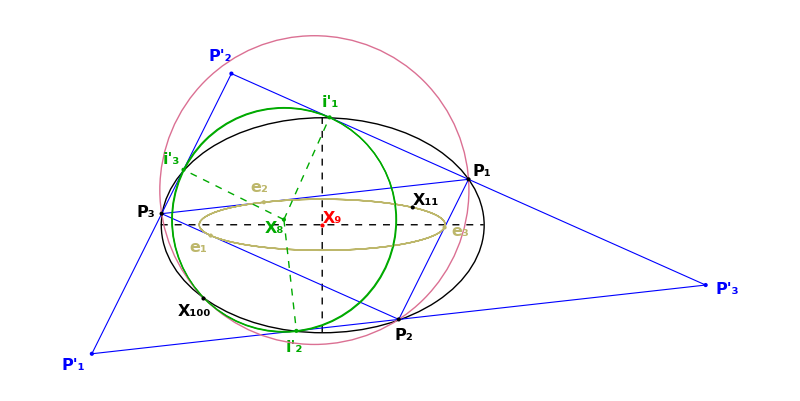

```mathematica
anticomlpPlot=showAntiCompl[1.5,25]
```

```mathematica
export3["0048_act_intouch",anticomlpPlot];
```

#### Anticomplementary Progress Along Billiard for Various Points

```mathematica
Clear@getAngularProgress;
Options@getAngularProgress={"clean"->False,"degStep"->1.};
getAngularProgress[a_,OptionsPattern[]]:=Module[{ts,ons,os,osSides,degStep=OptionValue@"degStep",
p1ths,p2ths,p3ths,
causticA,causticB,
osFs,osFths,
etts,ettTpths1,ettTpths2,ettTpths3,
acts,actSides,
actFs,actFths,
actTps,actTpths1,actTpths2,actTpths3},
ts=Range[0,360-degStep,degStep];
ons=orbitNormals[a,toRad@#]&/@ts;
os=First/@ons;
osSides=Third/@ons;
p1ths=toDeg[getBilliardAngle[a,1,#[[1]]]]&/@os;
p2ths=toDeg[getBilliardAngle[a,1,#[[2]]]]&/@os;
p3ths=toDeg[getBilliardAngle[a,1,#[[3]]]]&/@os;
(* these move along caustic *)
{causticA,causticB}=getTriCausticParams[a];
osFs=MapThread[getFeuerbachTrilin[#1,#2]&,{os,osSides}];
osFths=toDeg[getBilliardAngle[causticA,causticB,#]]&/@osFs;
etts=MapThread[extouchTriangle[#1,#2]&,{os,osSides}];
ettTpths1=toDeg[getBilliardAngle[causticA,causticB,#[[1]]]]&/@etts;
ettTpths2=toDeg[getBilliardAngle[causticA,causticB,#[[2]]]]&/@etts;
ettTpths3=toDeg[getBilliardAngle[causticA,causticB,#[[3]]]]&/@etts;

(* these sweep billiard {a Cos[t], Sin[t]} *)
acts=MapThread[anticomplementaryTriangle[#1,#2]&,{os,osSides}];
actSides=RotateLeft/@(triLengths/@acts);
actFs=MapThread[getFeuerbachTrilin[#1,#2]&,{acts,actSides}];
actTps=MapThread[intouchTriangle[#1,#2]&,{acts,actSides}];
actFths=toDeg[getBilliardAngle[a,1,#]]&/@actFs;
actTpths1=toDeg[getBilliardAngle[a,1,#[[1]]]]&/@actTps;
actTpths2=toDeg[getBilliardAngle[a,1,#[[2]]]]&/@actTps;
actTpths3=toDeg[getBilliardAngle[a,1,#[[3]]]]&/@actTps;
Transpose[{ts,#}]&/@If[OptionValue@"clean",
{p1ths,
osFths,ettTpths1,
actFths,actTpths1},
{p1ths,p2ths,p3ths,
osFths,ettTpths1,ettTpths2,ettTpths3,
actFths,actTpths1,actTpths2,actTpths3}]];
```

```mathematica
Clear@getAngularProgressP1P2P3;
Options@getAngularProgressP1P2P3={"degStep"->1.};
getAngularProgressP1P2P3[a_,OptionsPattern[]]:=Module[{ts,ons,os,osSides,degStep=OptionValue@"degStep",
p1ths,p2ths,p3ths,
causticA,causticB
},
ts=Range[0,360-degStep,degStep];
ons=orbitNormals[a,toRad@#]&/@ts;
os=First/@ons;
osSides=Third/@ons;
p1ths=toDeg[getBilliardAngle[a,1,#[[1]]]]&/@os;
p2ths=toDeg[getBilliardAngle[a,1,#[[2]]]]&/@os;
p3ths=toDeg[getBilliardAngle[a,1,#[[3]]]]&/@os;
(* these move along caustic *)
{causticA,causticB}=getTriCausticParams[a];

(* these sweep billiard {a Cos[t], Sin[t]} *)

Transpose[{ts,#}]&/@{p1ths,p2ths,p3ths}];
```

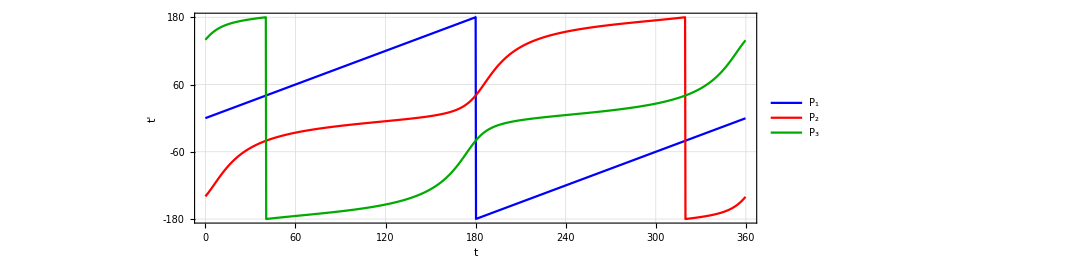

```mathematica
angularProgressP1P2P3Plot=ListLinePlot[getAngularProgressP1P2P3[1.5,"degStep"->.25],
PlotLegends->LineLegend[Style[#,16]&/@{
"P_1","P_2","P_3"},LegendLayout->{"Column",1}],
PlotStyle->{
{Thick,Blue},{Thick,Red},{Thick,Darker@Green}},
ImageSize->800,AspectRatio->.33,Frame->True,(*GridLines->Automatic,*)FrameStyle->Medium,
GridLines->Automatic,
PlotRange->{{0,360},{-180,180}},
FrameTicks->{{Range[-180,180,60],None},{Range[0,360,30],None}},
FrameLabel->(Style[#,{Black,16}]&/@{"t","t'"})(*,
PlotLabel->Style["Angular Progress for N=3 Orbit Points",{Black,Large}]*)]
```

```mathematica
export3["1105_pics_angular_progress_p1p2p3",angularProgressP1P2P3Plot]
```

```mathematica
showTrilinWithP1P2P3[a_,trilinFn_,n_]:=Module[{degStep=.1,eps=.0001,ts,lp,xs,ons,legend},
ts=Range[0,360-degStep,degStep]+eps;
ons=orbitNormals[a,toRad@#]&/@ts;
xs=MapThread[{#2,toDeg[getBilliardAngle[a,1,trilinFn[First@#1,Third@#1]]]}&,{ons,ts}];
lp=ListLinePlot[getAngularProgressP1P2P3[a,"degStep"->.25],(*,
PlotLegends->LineLegend[Style[#,16]&/@{
"P_1","P_2","P_3",ToString[Subscript["X",n],StandardForm]},LegendLayout->{"Column",1}],*)
PlotStyle->{
{Thick,Blue},{Thick,Red},{Thick,Darker@Green},{Dashed,Thick, Purple}},
ImageSize->800,AspectRatio->.33,Frame->True,(*GridLines->Automatic,*)FrameStyle->Medium,
PlotRange->{{0,360},{-180,180}},
FrameTicks->{{Range[-180,180,60],None},{Range[0,360,30],None}},
FrameLabel->(Style[#,{Black,16}]&/@{"t","t'"}),
Epilog->{Dashed,Purple,Thick,Line@xs}];
Legended[Show[lp,ImageSize->800,GridLines->Automatic,PlotLabel->Style["a/b="<>nfn[a,2],{Large,Black}]],LineLegend[Directive[{Thickness@Large,#}]&/@
{Blue,Red,Darker@Green,{Dashed, Purple}},
Style[#,16]&/@{
"P_1","P_2","P_3",ToString[Subscript["X",n],StandardForm]},LegendLayout->{"Column",1}]]]
```

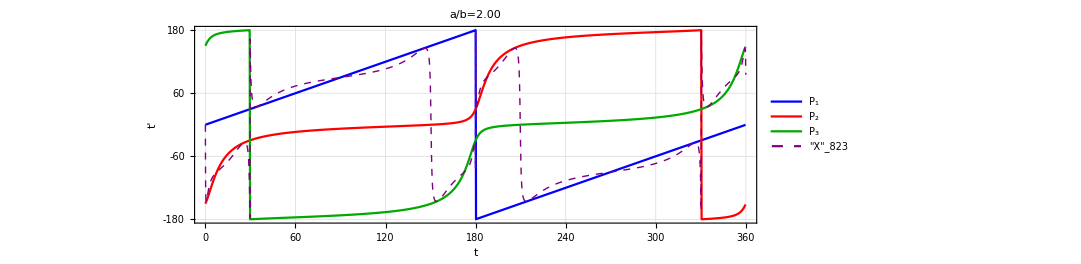

```mathematica
showTrilinWithP1P2P3[2,getX823Trilin,823]
```

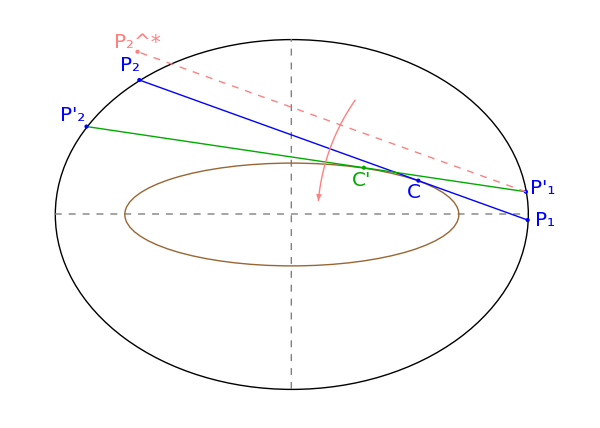

```mathematica
causticProgressPlot=Module[{a=1.35,tDeg=130.,ons,onsDt,dt=20.,ell,caustic,ac,bc,gr,ext,extDt,pQ,arc,arcR=1.2,arcStart,arcEnd},
{ac,bc}=getCausticAxes[a,1];
ell=plotEllAxes[a,{Thick,Black}];
caustic=plotEllb[ac,bc,{Thick,Brown}];
ons=orbitNormals[a,toRad@tDeg];
ext=extouchTriangle[ons[[1]],ons[[3]]];
onsDt=orbitNormals[a,toRad@(tDeg+dt)];
extDt=extouchTriangle[onsDt[[1]],onsDt[[3]]];
pQ=onsDt[[1,2]]-ons[[1,2]]+ons[[1,1]];
arcStart=toRad@145.;
arcEnd=toRad@175.;
arc=Table[ons[[1,2]]+arcR{Cos@t,Sin@t},{t,arcStart,arcEnd,.01}];
gr=Graphics[{PointSize@Large,FaceForm@None,Arrowheads@Large,
{Thick,Blue,Line@{ons[[1,1]],ons[[1,2]]},Blue,Point@{ons[[1,1]],ons[[1,2]]}},
{Thick,Darker@Green,Line@{onsDt[[1,1]],onsDt[[1,2]]},Blue,Point@{onsDt[[1,1]],onsDt[[1,2]]}},
{Thick,Dashed,Pink,Line@{onsDt[[1,2]],pQ},Text[Style[Superscript["P_2","*"],20],pQ,{0,-1.5}],Point@pQ},
{Thick,Pink,Arrow@arc},
{Blue,Point@ext[[3]],Darker@Green,Point@extDt[[3]]},
{Blue,{ellLabelPoints[a,Part[ons[[1]],{2,1}],"P",20,.1]}},
{Blue,{ellLabelPoints[a,Part[onsDt[[1]],{2,1}],"P'",20,.1]}},
{Blue,ellLabelTxtb[ac,bc,ext[[3]],Style["C",20],.075,inward->True]},
{Darker@Green,ellLabelTxtb[ac,bc,extDt[[3]],Style["C'",20],.075,inward->True]}
}];
Show[{ell,caustic,gr},ImageSize->600]]
```

```mathematica
export3["1110_caustic_progress",causticProgressPlot]
```

### ACT EKG

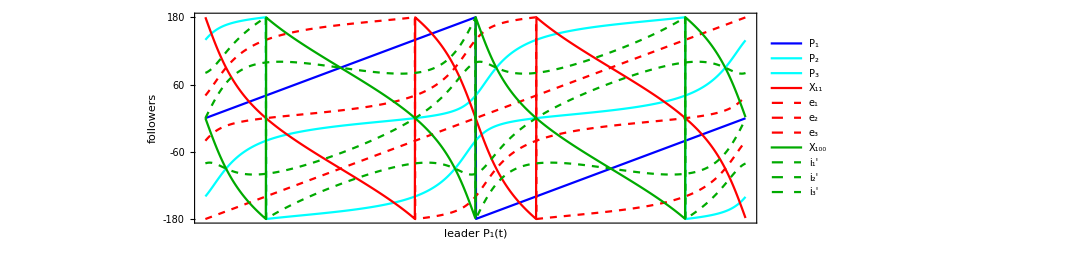

```mathematica
angularProgressPlot=ListLinePlot[getAngularProgress[1.5,"degStep"->.25],
PlotLegends->LineLegend[Style[#,16]&/@{
"P_1","P_2","P_3",
"X_11","e_1","e_2","e_3",
"X_100","i_1'","i_2'","i_3'"
},LegendLayout->{"Column",1}],
PlotStyle->{
{Thick,Blue},Sequence@@ConstantArray[Cyan,2],
Red,Sequence@@ConstantArray[{Dashed,Red},3],
Darker@Green,Sequence@@ConstantArray[{Dashed,Darker@Green},3]},
ImageSize->800,AspectRatio->.33,Frame->True,(*GridLines->Automatic,*)FrameStyle->Medium,
PlotRange->{{0,360},{-180,180}},
FrameTicks->{{Range[-180,180,60],None},{None,Range[0,360,60]}},
FrameLabel->(Style[#,{Black,16}]&/@{"leader P_1(t)","followers"})(*,
PlotLabel->Style["Angular Progress for N=3 Orbit Points",{Black,Large}]*)]
```

```mathematica
export3["0049_act_progress",angularProgressPlot];
```

```mathematica
Clear@getAngularPogressI1Diff;getAngularPogressI1Diff[a_,degStep_,yfact_:1]:=Module[{i1,i1t,i1v,i1vd},
i1=getAngularProgress[a,"degStep"->degStep,"clean"->True][[5]];
i1t=First/@i1;
i1v=Second/@i1;
i1vd=yfact Differences[i1v];
MapThread[{#1,#2}&,{Most@i1t,i1vd}]];
```

```mathematica
getAngPP[a_]:=Module[{degStep=.25,i1diff,llp},
i1diff=getAngularPogressI1Diff[a,degStep,500];
ListLinePlot[
Append[getAngularProgress[a,"degStep"->degStep,"clean"->True],i1diff],
PlotLegends->LineLegend[Style[#,16]&/@{
"P_1",
"X_11","e_1",
"X_100","i_1'","vel(i1')"
},LegendLayout->{"Column",1}],
PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Dashed,Blue},{Thick,Dashed,Red},{Darker@Green,Thick},{Dashed,Thick,Darker@Green}},
PlotLabel->Style["a="<>nfn[a,3],{Black,16}],
ImageSize->800,AspectRatio->.33,Frame->True,(*GridLines->Automatic,*)FrameStyle->Medium,
PlotRange->{{0,360},{-180,180}},
GridLines->{Range[0,360,30],Range[-180,180,30]},
FrameTicks->{{Range[-180,180,60],None},{Range[0,360,30],None}},
FrameLabel->(Style[#,{Black,16}]&/@{"t","t'"})(*,
PlotLabel->Style["Angular Progress for N=3 Orbit Points",{Black,Large}]*)]];
```

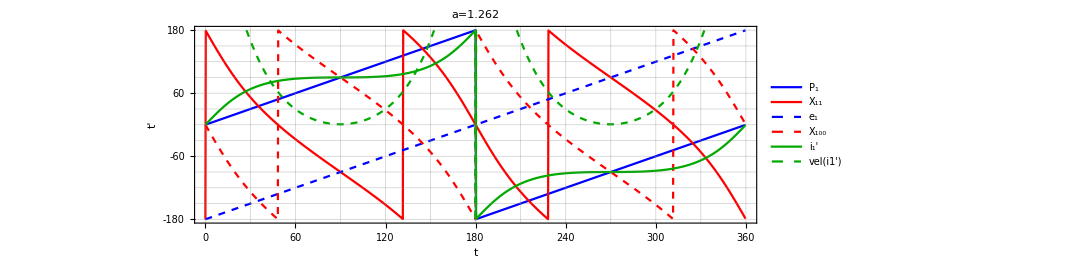

```mathematica
angularProgressPlotClean1265=getAngPP[1.262]
```

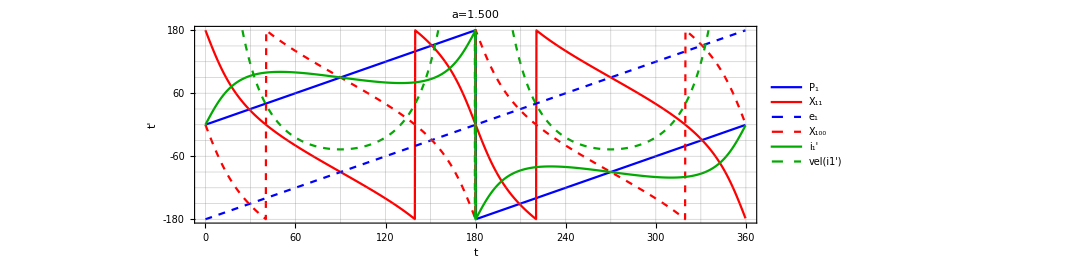

```mathematica
angularProgressPlotClean15=getAngPP[1.5]
```

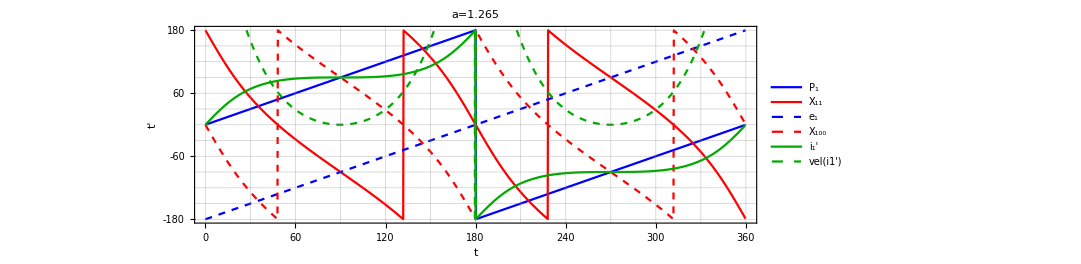
-Graphics-
-Graphics-

```mathematica
angularProgressPlotBoth=Grid[{{angularProgressPlotClean1265},
{angularProgressPlotClean15}}]
```

```mathematica
export3["0050_act_progress_clean_1265",angularProgressPlotClean1265];
```

```mathematica
export3["0049_act_progress_clean_15",angularProgressPlotClean15];
```

```mathematica
export3["0051_act_progress_clean_both",angularProgressPlotBoth];
```

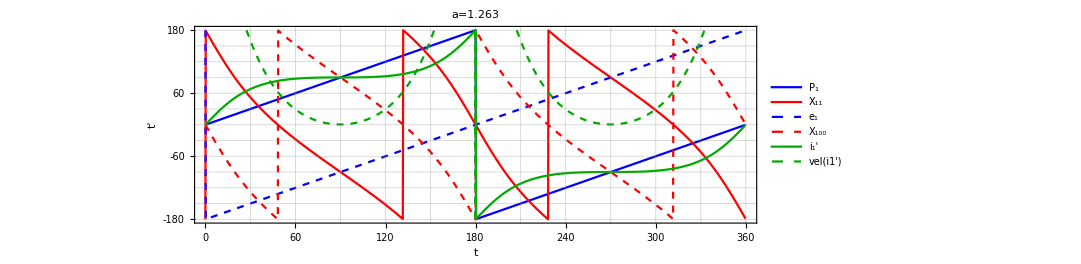

```mathematica
angularProgressPlotClean1263=getAngPP[1.263]
```

```mathematica
export3["0049_act_progress_clean_1263",angularProgressPlotClean1263];
```

#### Symmedian Quartic

```mathematica
Clear@t
```

```mathematica
Clear@showSymmErr;
Options@showSymmErr={symClr->Darker@Red,idealClr->Darker@Green,factor->10^7,fontSize->20};showSymmErr[a_,tDeg2_,OptionsPattern[]]:=Module[{o,n,s,a6,b6,denom,gr,x6,x6i,x6mult,gr2,ell,t,b=1,δ,ell6,degStep=.25,tDegMax=360,x6s,x6sInter,x6sMult},
x6s=Table[t=toRad@tDeg;{o,n,s}=orbitNormals[a,t];getSymmedianTrilin[o,s],{tDeg,0,tDegMax-degStep,degStep}];
δ=Sqrt[a^4-a^2*b^2+b^4];
denom=(3*a^4-2*a^2*b^2+3*b^4);
a6=(-b^4-a^2*b^2-δ*b^2+3*δ*a^2)*a/denom;
b6=(a^4+b^2*a^2+δ*a^2-3*δ*b^2)*b/denom;
x6sInter=ellInterRaybUnprot[a6,b6,#,-#][[1]]&/@x6s;
x6sMult=MapThread[ray[#1,#2-#1,OptionValue@factor*magn[#2-#1]]&,{x6sInter,x6s}];
ell6=Table[t=toRad@tDeg;{a6 Cos@t,b6 Sin@t},{tDeg,0,tDegMax-degStep,degStep}];
gr=Graphics[{PointSize@Large,
{Black,Point@{0,0},Text[Style["O",OptionValue@fontSize],{0,0},{0,-1.5}]},
{Thick,OptionValue@idealClr,Line@ell6},
{OptionValue@symClr,Thick,Dashed,Line@x6sMult}}];
ell=plotEll[a,{Thick,Black}];
{o,n,s}=orbitNormals[a,toRad@tDeg2];
x6=getSymmedianTrilin[o,s];
x6i=ellInterRaybUnprot[a6,b6,x6,-x6][[1]];
x6mult=ray[x6i,x6-x6i,OptionValue@factor*magn[x6-x6i]];
gr2=Graphics[{PointSize@Large,FaceForm@None,
{Black,Thick,Line@{{0,0},x6mult},ellLabelTxt[a,o[[1]],Style["P_1(t)",OptionValue@fontSize],.1]},
{EdgeForm@{Thick,Blue},Polygon@o},
{Darker@Green,Point@x6,Text[Style["X_6",OptionValue@fontSize],x6i,{.25,1.5}],Blue,Point@o[[1]],OptionValue@symClr,Point@x6mult,Text[Style["~X_6",OptionValue@fontSize],x6,{-1.5,-1.25}]}}];
Show[{ell,gr,gr2},PlotRange->{{-1.6,1.6},{-1.1,1.1}},ImageSize->800]];
```

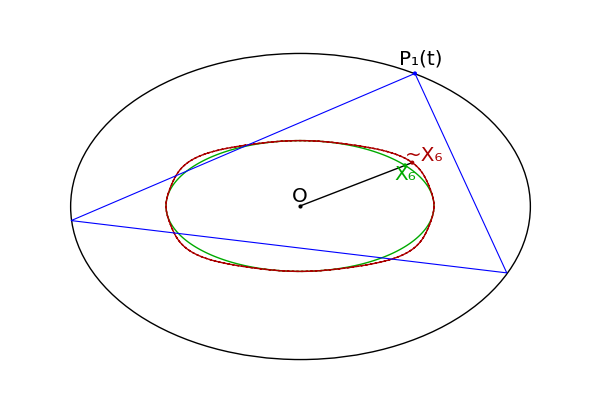

```mathematica
symmQuarticPlot=Show[showSymmErr[1.5,60.,factor->2.*10^6],ImageSize->600]
```

```mathematica
export3["0041_symmedian",symmQuarticPlot];
```

```mathematica
Clear@makeRadiiGraphPlot;
Options@makeRadiiGraphPlot={ylabel->None,legendPlacement->Left};
makeRadiiGraphPlot[a_,OptionsPattern[]]:=Module[{degStep=1,ons,rads,o,s,llp,clrs=(#/.ptClrs)&/@{"inc","cir","npc"},ps,epi,lgd},
ons=Table[orbitNormals[a,toRad@deg],{deg,0,360-degStep,degStep}];
rads={getInradius@#,getCircumradius@#,getNinepointCircleRadius@#}&/@Third/@ons;
ps={Thick,#}&/@clrs;
epi={Dashed,"cir"/.ptClrs,Arrowheads[{-.03,.03}],Arrow@{{90,1.15},{90,2.3}},Text[Style["R/r_9=2",16],{90,.5(1.15+2.3)},{-1.25,1}],
"inc"/.ptClrs,Arrowheads[{-.03,.03}],Arrow@{{270,.55},{270,2.3}},
Text[Style["R/r=???",Large],{270,.5(1.15+2.3)},{-1.25,1}]};
llp=ListLinePlot[Transpose@rads,Frame->True,FrameStyle->{{Black,Medium},{Black,Medium}},
PlotLabel->Style["a="<>nfn[a,1]<>", b=1",{Black,Large}],FrameLabel->{Style["t",{Black,Large}],OptionValue@ylabel},FrameTicksStyle->16,Epilog->epi,PlotStyle->ps,ImageSize->Large,PlotRange->{Automatic,Automatic}];
Legended[llp,Placed[LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
Style[#,Large]&/@{"r","R","r_9"}],OptionValue@legendPlacement]]]
```

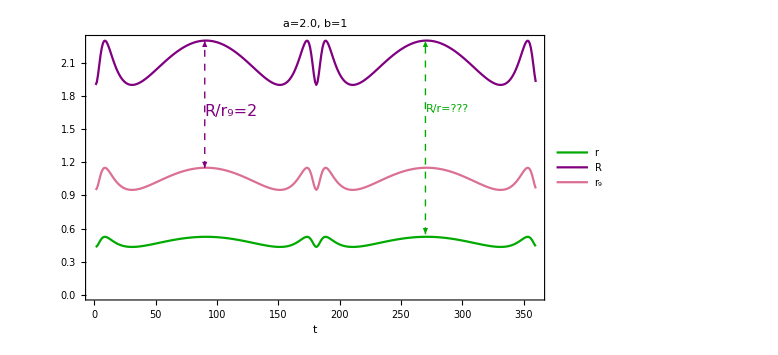

```mathematica
radiiGraphPlot=makeRadiiGraphPlot[2.]
```

```mathematica
export3["0075_radii_plot",radiiGraphPlot];
```

```mathematica
minMaxrR[a_,b_]:=Module[{δ,c2,Rmin,Rmax,rmin,rmax},
δ=Sqrt@(a^4-a^2*b^2+b^4);
c2=a^2-b^2;
Rmin=(a^2+δ)/(2a);
Rmax=(b^2+δ)/(2b);
rmin=(δ-b^2)b^2/(c2 a);
rmax=(a^2-δ)a^2/(c2 b);
<|"Rmin"->Rmin,"Rmax"->Rmax,"rmin"->rmin,"rmax"->rmax|>
];
```

```mathematica
{"Rmin","rmin"}/.minMaxrR[1.5,1]
```

{1.40085,0.508033}

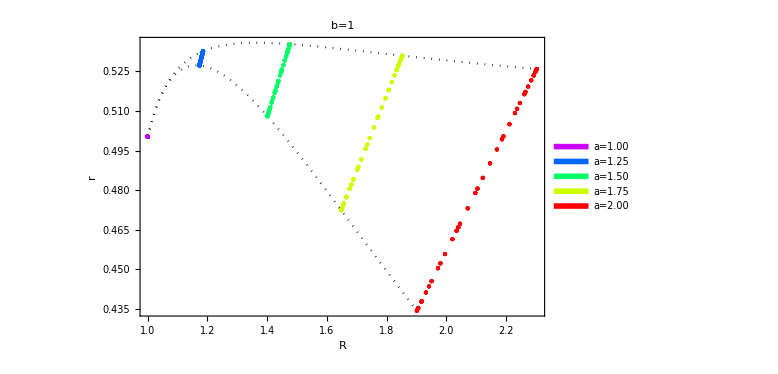

```mathematica
radiiScatterPlot=Module[{degStep=2.5,as={1.001,1.25,1.5,1.75,2.},ons,rads,o,s,lp,Rr,Rr9,clrs,lab,rmin,parMin,parMax},
ons=Table[orbitNormals[#,toRad@deg],{deg,0,360-degStep,degStep}]&/@as;
rads=Table[{getInradius@#,getCircumradius@#,getNinepointCircleRadius@#}&/@Third/@ons[[i]],{i,Length@ons}];
Rr=Table[{#[[2]],#[[1]]}&/@rads[[i]],{i,Length@rads}];
Rr9=Table[{#[[2]],#[[3]]}&/@rads[[i]],{i,Length@rads}];
parMin=ParametricPlot[{"Rmin","rmin"}/.minMaxrR[a,1],{a,First@as,Last@as},PlotStyle->{Dotted,Black}];
parMax=ParametricPlot[{"Rmax","rmax"}/.minMaxrR[a,1],{a,First@as,Last@as},PlotStyle->{Dotted,Black}];
clrs=Hue[1-#/Length@as]&/@Range[Length@as];
lp=Show[{parMin,parMax,Table[Graphics[{PointSize@Medium,clrs[[i]],Point@Rr[[i]]}],{i,Length@rads}]},Axes->False,
PlotLabel->Style["b=1",{Black,Large}],PlotRange->All,Frame->True,FrameStyle->{{Black,Medium},{Black,Medium}},AspectRatio->.65,FrameTicksStyle->16, ImageSize->Large,FrameLabel->(Style[#,{Black,Large}]&/@{"R","r"})];
Legended[lp,LineLegend[Directive[{Thickness@.0125,#}]&/@clrs,
Style["a="<>nfn[#,2],16]&/@as]]]
```

```mathematica
radiiGrid=Grid[{{radiiGraphPlot,radiiScatterPlot}}]
```

-Graphics- | -Graphics-

```mathematica
export3["0080_radii_grid",radiiGrid];
```

```mathematica
drawSimRovR[a_,tDeg_]:=Module[{ell,ons,gr,lab,r,R,x1,x3,clrs},
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@tDeg];
r=getInradius[ons[[3]]];
R=getCircumradius[ons[[3]]];
x1=getIncenterTrilin[ons[[1]],ons[[3]]];
x3=getCircumcenterTrilin[ons[[1]],ons[[3]]];
clrs={"inc"/.ptClrs,"cir"/.ptClrs};
gr=Graphics@{FaceForm@None,PointSize@Large,
{Gray,Dashed,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
{EdgeForm@{Thick,Blue},Polygon@ons[[1]]},
MapThread[{#3,Point@#2,Text[Style[Subscript["X",#1],{20}],#2,{1.25,-1.25}]}&,{{1,3},{x1,x3},clrs}],
MapThread[{Thick,#1,Circle[#2,#3]}&,{clrs,{x1,x3},{r,R}}]};
lab="a="<>nfn[a,2]<>", θ="<>nfn[tDeg,2]<>"°\nr="<>nfn[r,3]<>", R="<>nfn[R,3]<>", r/R="<>nfn[r/R,3];
Show[{ell,gr},PlotLabel->Style[lab,16]]];
```

```mathematica
getX1X3loci[a_]:=Module[{locusX1,locusX3,ons,eps=.001},
locusX1=Quiet@ParametricPlot[ons=orbitNormals[a,t+eps];getIncenterTrilin[ons[[1]],ons[[3]]],{t,0,π/1.2},PlotStyle->{Dashed,"inc"/.ptClrs}];
locusX3=Quiet@ParametricPlot[ons=orbitNormals[a,t+eps];getCircumcenterTrilin[ons[[1]],ons[[3]]],{t,0,π/1.2},PlotStyle->{Dashed,"cir"/.ptClrs}];
{locusX1,locusX3}];
```

```mathematica
Manipulate[
DynamicModule[{locusX1,locusX3,ons,eps=.001},
{locusX1,locusX3}=getX1X3loci[a];
Dynamic[Show[{drawSimRovR[a,tDeg],locusX1,locusX3},ImageSize->Large,PlotRange->{{-3,3},{-2,2}}]]],
{{a,2},1.01,3,.01},{{tDeg,0.},-180,180,.25}]
```

Set::shape: Lists {locusX1$20970, locusX3$20970} and getX1X3loci[2] are not the same shape.

Set::shape: Lists {locusX1$52143, locusX3$52143} and getX1X3loci[2] are not the same shape.

Set::shape: Lists {locusX1$440923, locusX3$440923} and getX1X3loci[2] are not the same shape.

Set::shape: Lists {locusX1$1294322, locusX3$1294322} and getX1X3loci[2] are not the same shape.

Set::shape: Lists {locusX1$40784, locusX3$40784} and getX1X3loci[2] are not the same shape.

Set::shape: Lists {locusX1$51062, locusX3$51062} and getX1X3loci[2] are not the same shape.

Set::shape: Lists {locusX1$84506, locusX3$84506} and getX1X3loci[2] are not the same shape.

Set::shape: Lists {locusX1$60245, locusX3$60245} and getX1X3loci[2] are not the same shape.

Set::shape: Lists {locusX1$1780696, locusX3$1780696} and getX1X3loci[2] are not the same shape.

Set::shape: Lists {locusX1$1166108, locusX3$1166108} and getX1X3loci[2] are not the same shape.

Set::shape: Lists {locusX1$2355424, locusX3$2355424} and getX1X3loci[2] are not the same shape.

Set::shape: Lists {locusX1$163166, locusX3$163166} and getX1X3loci[2] are not the same shape.

Set::shape: Lists {locusX1$53867, locusX3$53867} and getX1X3loci[2] are not the same shape.

Set::shape: Lists {locusX1$2202947, locusX3$2202947} and getX1X3loci[2] are not the same shape.

```mathematica
drawSimRovRandX1X3Loci[a_,tDeg_]:=Module[{pRr,loci},
loci=getX1X3loci[a];
pRr=drawSimRovR[a,tDeg];
Show[{pRr,loci}]];
```

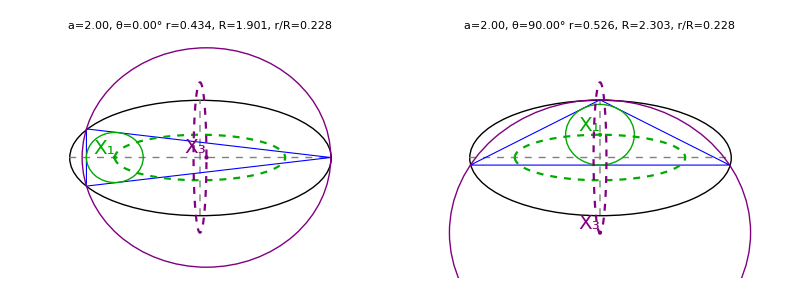

```mathematica
minMaxOrbits=Grid[{MapThread[Show[#2,ImageSize->{400,400},PlotRange->{{-#1,#1},{-2,2}}]&,{{2.5,2.5},{drawSimRovRandX1X3Loci[2.,0],drawSimRovRandX1X3Loci[2.,90.]}}]},Spacings->0]
```

```mathematica
export3["0081_radii_min_max_orbits",minMaxOrbits];
```

```mathematica
Clear@getSumProdCosines;
getSumProdCosines[a_,tDeg_]:=Module[{o,n,s,exc,prod,cosSum,excCosProd},
{o,n,s}=orbitNormals[a,toRad@tDeg];
cosSum=Total@getTriCosines@o;
exc=excentralTriangle[o,s];
excCosProd=Apply[Times,getTriCosines@exc];
{cosSum,excCosProd}];
```

#### Sum of Cosines Divided by Product of Cosines vs a/b

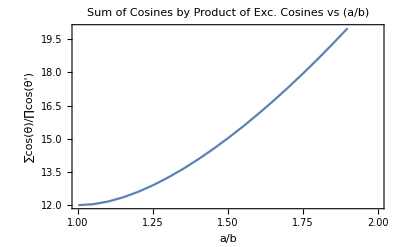

```mathematica
Module[{sp},
ListLinePlot[Table[sp=getSumProdCosines[a,0];{a,sp[[1]]/sp[[2]]},{a,1.001,2,.05}],Frame->True,PlotLabel->Style["Sum of Cosines by Product of Exc. Cosines vs (a/b)",{Black,Medium}],FrameStyle->15,PlotRange->{{1,2},{12,20}},FrameLabel->{"a/b","∑cos(θ)/∏cos(θ')"}]]
```

```mathematica
Clear@getRadiusRatio;
getRadiusRatio[a_,tDeg_]:=Module[{o,n,s},
{o,n,s}=orbitNormals[a,toRad@tDeg];
(getInradius@s/getCircumradius@s)];
```

```mathematica
Module[{aInfl= 1.372851,ratioInfl},
ratioInfl=getRadiusRatio[aInfl,0];
ratioInfl]
```

0.406909

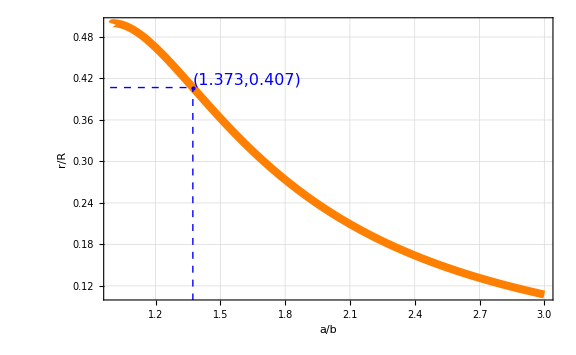

```mathematica
rRvsabPlot=Module[{o,n,s,pl,aInfl,ratioInfl,pInfl},
aInfl= 1.372851;
ratioInfl=getRadiusRatio[aInfl,0];
pInfl={aInfl,ratioInfl};
pl=Quiet@Plot[getRadiusRatio[a,0],{a,1,3},PlotStyle->{Thickness@.01,Orange},Frame->True,FrameTicksStyle->Large,FrameLabel->(Style[#,{Large,Black}]&/@{"a/b","r/R"}),GridLines->Automatic,Epilog->{PointSize@Large,Blue,Point@pInfl,Dashed,Line@{{aInfl,0},pInfl},Line@{{0,ratioInfl},pInfl},Text[Style["("<>nfn[pInfl[[1]],3]<>","<>nfn[pInfl[[2]],3]<>")",16],pInfl,{-1,-1.5}]}];
Show[pl,ImageSize->Large]]
```

```mathematica
export3["0082_rR_vs_ab",rRvsabPlot]
```

```mathematica
radiiGrid2=Grid[{{makeRadiiGraphPlot[2.,legendPlacement->Right,ylabel->""]},{radiiScatterPlot}},Alignment->Center]
```

-Graphics-
-Graphics-

```mathematica
export3["0083_radii_grid2",radiiGrid2]
```

```mathematica
NSolve[9*k^12-18*k^10-k^8+16*k^6-21*k^4+2*k^2+1==0,k]
```

{{k→-1.37285},{k→-0.879235-0.469004 ⅈ},{k→-0.879235+0.469004 ⅈ},{k→-0.559964},{k→0.-0.409553 ⅈ},{k→0.+0.409553 ⅈ},{k→0.-1.06617 ⅈ},{k→0.+1.06617 ⅈ},{k→0.559964},{k→0.879235-0.469004 ⅈ},{k→0.879235+0.469004 ⅈ},{k→1.37285}}

```mathematica
Sqrt/@Flatten[Values/@NSolve[9*k^6-18*k^5-k^4+16*k^3-21*k^2+2*k+1==0,k]]
```

{0.+1.06617 ⅈ,0.+0.409553 ⅈ,0.559964,0.879235-0.469004 ⅈ,0.879235+0.469004 ⅈ,1.37285}

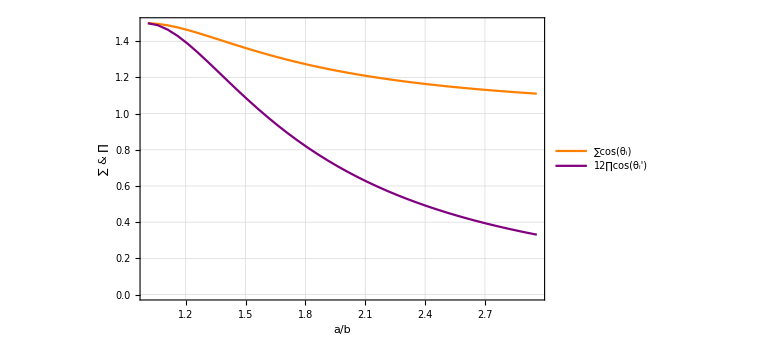

```mathematica
Module[{o,n,s,pl,sp},
pl=ListLinePlot[Transpose@Table[sp=getSumProdCosines[a,0];{{a,sp[[1]]},{a,12sp[[2]]}},{a,1.01,3,.05}],PlotStyle->{{Thick,Orange},{Thick,Purple}},Frame->True,FrameStyle->ConstantArray[{Black,12},4],ImageSize->Large,GridLines->Automatic,FrameLabel->(Style[#,{Large,Black}]&/@{"a/b","∑ & ∏"})];
Show[Legended[pl,LineLegend[Directive[{Thickness@Large,#}]&/@{Orange,Purple},{"∑cos(θ_i)","12∏cos(θ_i')"}]]]]
```

#### derived tris

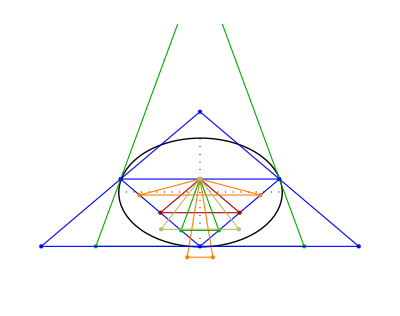
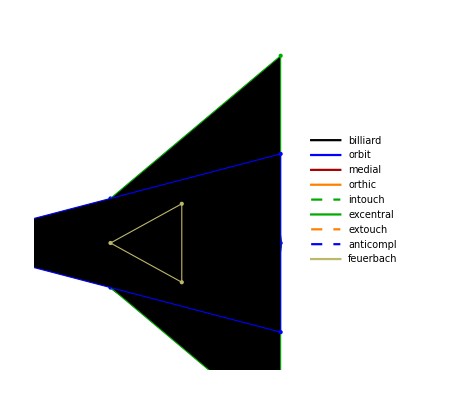
-Graphics- | -Graphics-

```mathematica
lemma3plot=Module[{pl1,pl2},
pl1=showDerivedTris[1.5,-90.,drLegends->False,drCaustic->False];
pl2=showDerivedTris[1.5,0.,drLegends->True,drCaustic->False];
Grid[{MapThread[Show[#1,PlotLabel->None,Frame->None,PlotRange->{#2,{-1.75,3}},ImageSize->{Automatic,400}]&,{{pl1,pl2},{{-3,3},{-2.25,1.75}}}]},Spacings->0]]
```

```mathematica
export3["0072_lemma3",lemma3plot]
```

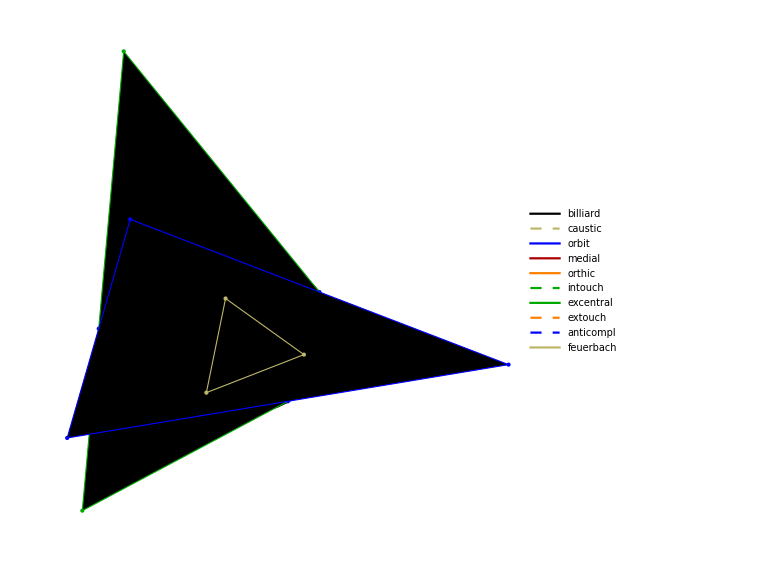

```mathematica
derivedTrisPlot=Show[showDerivedTris[1.5,30],PlotRange->All,Frame->None,PlotLabel->None]
```

```mathematica
export3["0043_derived-triangles",derivedTrisPlot];
```

#### Billiard Trajectories: needs to to to ngons_v1.nb

```mathematica
Clear@makeTrilinPlot;
makeTrilinPlot[a_,tDeg_,kimbN_]:=Module[{ons,gr,X,pedalTri,medialTri,medialPedals,trils},
ons=orbitNormals[a,toRad@tDeg];
{X,trils}=Part[First@getNewCenters[ons[[1]],ons[[3]],{kimbN}],{3,4}];
pedalTri=pedalTriangle[ons[[1]],ons[[3]],trils];
(* &&& *)
medialTri=medialTriangle[ons[[1]],ons[[3]]];
medialPedals=(X+#)/2&/@pedalTri;
gr=Graphics[{FaceForm@None,Thick,PointSize@Large,
{EdgeForm@{Thick,Blue},Polygon@ons[[1]],Blue,Point@ons[[1]]},
{Dashed,Darker@Red,Line@{X,#}&/@pedalTri},
{Darker@Green,Point@X,Text[Style["X",{20}],X,{-2,-.5}]},
{Red,Point@pedalTri},
{ellLabelPoints[a,ons[[1]],"P",20,.1]},
{MapThread[Text[Style[#1,20],#2,#3]&,{{"s_1","s_2","s_3"},medialTri,{{1,1},{1.75,-1.75},{-1,1}}}]},
{MapThread[Text[Style[#1,20],#2,#3]&,{{"p","q","r"},medialPedals,{{1,-1},{1.5,0},{-2,-.75}}}]}}];
Show[gr,ImageSize->Large]];
```

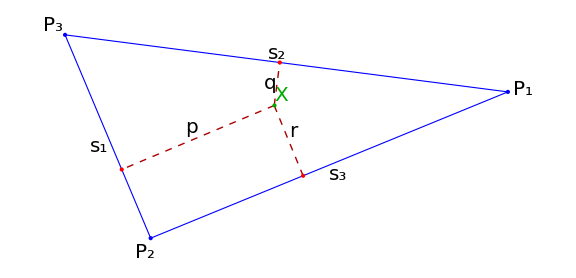

```mathematica
trilinPlotPos=makeTrilinPlot[1.5,5,9]
```

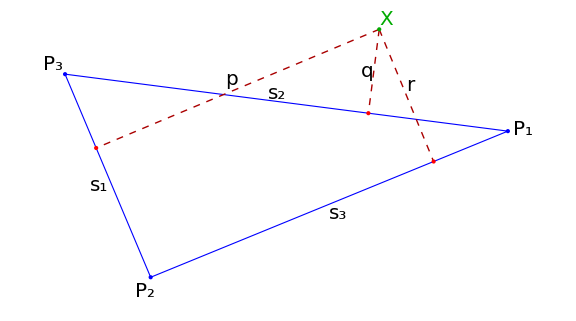

```mathematica
trilinPlotNeg=makeTrilinPlot[1.5,5,40]
```

```mathematica
export3["1120_trilins",Grid[{{trilinPlotPos,trilinPlotNeg}}]]
```

```mathematica
Clear@showOrthicIncenter;
Options@showOrthicIncenter={drObtuse->False};
showOrthicIncenter[u_,v_,OptionsPattern[]]:=Module[{ref,refSides,el,ort,gr,x4,k=1.33},
ref={{0,0},{1,0},{u,v}};
refSides=triLengthsRL@ref;
x4=getOrthocenterTrilin[ref,refSides];
ort=orthicTriangle[ref,refSides];
gr=Graphics[{PointSize@Large,FaceForm@None,
{EdgeForm@{Thick,Blue},Polygon@ref,Blue,Point@ref},
{Dashed,Black,MapThread[Line@{#1,#2}&,{ref,ort}]},
If[OptionValue@drObtuse,{Dashed,Black,Line@{#,x4}&/@ReplacePart[ort,2->ref[[2]]]},{}],
If[OptionValue@drObtuse,{Dashed,Black,Line@{ref[[2]],#}&/@Part[ort,{1,3}]},{}],
{EdgeForm@{Thick,Orange},Polygon@ort,Orange,Point@ort},
{Orange,Point@x4,Text[Style[If[OptionValue@drObtuse,"X_4","X_4=X_1'"],20,Background->White],x4,If[!OptionValue@drObtuse,{0,-k},{-1.25k,0}]]},
{Blue,Style[#,20,Background->White]&/@MapThread[Text[#1,#2,#3]&,{{"A",If[!OptionValue@drObtuse,"B","B=X_1'"],"C"},ref,{{0,k},If[!OptionValue@drObtuse,{0,k},{0,1.25k}],{0,-k}}}]},
{Orange,Style[#,20]&/@MapThread[Text[#1,#2,#3]&,{{"A'","B'","C'"},ort,
If[!OptionValue@drObtuse,
{{-1.5k,0},{0,-k},{0,k}},
{{0,1.25k},{0,-k},{-1.5k,0}}]
}]}}];
Show[gr,ImageSize->400]];
```

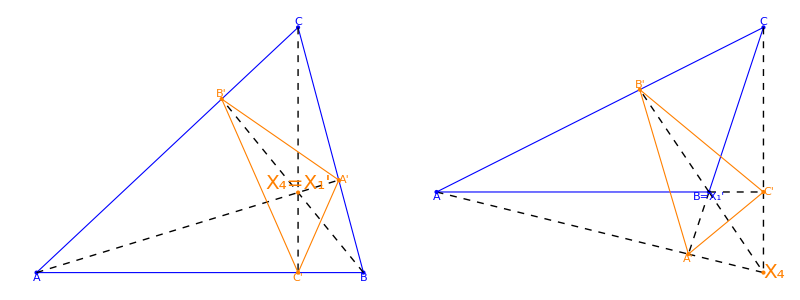

```mathematica
orthicIncenterPlot=Grid[{{showOrthicIncenter[.8,.7],showOrthicIncenter[1.2,.7,drObtuse->True]}}]
```

```mathematica
export4["1180_orthic_incenter",orthicIncenterPlot]
```